論文とnotebookの軸名 / Axis names in the manuscript and notebook

論文の Front と Back は，この notebook ではそれぞれ In と Out と呼ぶ．したがって，論文の Back–Front 軸は notebook の Out–In 軸に対応する．
In this notebook, the manuscript’s Front and Back are labeled In and Out, respectively. Thus, the manuscript’s Back–Front axis corresponds to the notebook’s Out–In axis.

Front（manuscript）= In（this notebook）
Back（ manuscript）= Out（this notebook）

```mathematica
baseDir=DirectoryName[NotebookDirectory[]];
dirw=FileNameJoin[{baseDir,"VAE_weight_mandarin3D"}]<>$PathnameSeparator;
```

```mathematica
dir=baseDir<>$PathnameSeparator;
```

```mathematica
dataitem=Import[FileNameJoin[{baseDir,"shapeddata","mandarin_cdi_word_category_symbol_mapping.xls"}],"xls"][[1]];
```

```mathematica
dataunilemma=Import[FileNameJoin[{baseDir,"shapeddata","MandarinBeijing_WS_WordItems.csv"}],"csv"];
```

```mathematica
cl=ColorData["DefaultPlotColors","ColorList"];
```

```mathematica
(*CSVの第1列をバイアス，第2列以降を重み行列として読み込む．Import the first CSV column as the bias vector and the remaining columns as the weight matrix.*)importVAEParameters[file_String]:=Module[{table},table=Import[FileNameJoin[{dirw,file}],"CSV"];
{Transpose[table[[2;;,2;;]]],table[[2;;,1]]}];

(*学習済みEncoderとDecoderのパラメータを読み込む．Import the trained encoder and decoder parameters.*)
{wedE,wedbE}=importVAEParameters["VAEweD_mandarin3d.csv"];
{wezmE,wezmbE}=importVAEParameters["VAEweZm_mandarin3d.csv"];
{wezlvE,wezlvbE}=importVAEParameters["VAEweZlv_mandarin3d.csv"];
{wdd1E,wdd1bE}=importVAEParameters["VAEwdD1_mandarin3d.csv"];
{wdd2E,wdd2bE}=importVAEParameters["VAEwdD2_mandarin3d.csv"];
```

```mathematica
(*Mandarin CDIのwide形式CSVをヘッダー行を含めて読み込み，参加者IDと月齢を整数に変換する．Import the Mandarin CDI wide-format CSV including its header,and convert participant IDs and age to integers.*)datatmp=Import[FileNameJoin[{baseDir,"shapeddata","MandarinBeijing_WS_20230907_shaped_wide.csv"}],"CSV","HeaderLines"->0];

datatmp[[2;;,2;;4]]=Map[FromDigits,datatmp[[2;;,2;;4]],{2}];
```

```mathematica
(*ヘッダーを保持し，参加者データのCDI応答を0/1に変換する．Preserve the header and convert CDI responses to 0/1.*)alldata=Prepend[Rest[datatmp]/. {""->0,"produces"->1,"NA"->0,Missing[_]->0},First[datatmp]];
```

```mathematica
(*VAEに入力する799項目のCDI応答行列を取り出す．Extract the 799-item CDI response matrix used as VAE input.*)data=alldata[[2;;,5;;]];
```

```mathematica
d=Length[data[[1]]]
```

799

```mathematica
(*Mandarin CDI入力の行列サイズと0/1の内訳を確認する．Check the dimensions and binary response counts of the Mandarin CDI input.*)<|"ImportedDimensions"->Dimensions[datatmp],"DataDimensions"->Dimensions[data],"ItemCount"->d,"ResponseCounts"->Counts[Flatten[data]],"ResponseValues"->Union[Flatten[data]]|>
```

<|ImportedDimensions→{1057,803},DataDimensions→{1056,799},ItemCount→799,ResponseCounts→<|1→498341,0→345403|>,ResponseValues→{0,1}|>

```mathematica
relu[x_]:=Max[0,x]
```

```mathematica
(*CDI入力からEncoderの隠れ層と潜在平均を行列計算で求める．Compute the encoder hidden activations and latent means from the CDI matrix.*)denseE=Map[relu,data.wedE+ConstantArray[wedbE,Length[data]],{2}];
calcZ[hidden_,weight_,bias_]:=hidden.weight+ConstantArray[bias,Length[hidden]];

zdataE0=calcZ[denseE,wezmE,wezmbE];
```

```mathematica
(*同じ隠れ層から潜在事後分布の対数分散を求める．
Compute the latent posterior log variances from the same hidden activations.*)lσdataE0=calcZ[denseE,wezlvE,wezlvbE];
```

```mathematica
toz0[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezmE+wezmbE;
a
]
```

```mathematica
tologsigma0[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezlvE+wezlvbE;
a
]
```

```mathematica
predictorg[z_]:=LogisticSigmoid[((relu[#]&/@((z.wdd1E)+wdd1bE)).wdd2E+wdd2bE)]
```

#### 軸変換前のVAE潜在空間と等総語彙面 Original VAE latent space and isovocabulary surface before axis transformation

```mathematica
decallorg=Import[dirw<>"VAEdecAllMand3d.csv","csv"];
decallorg=ArrayReshape[decallorg,{799,30,30,30}];
```

```mathematica
Dimensions/@{zdataE0,lσdataE0}
```

{{1056,3},{1056,3}}

```mathematica
pz0=Show[
ListPointPlot3D[zdataE0,BoxRatios->1,PlotStyle->PointSize[0.008],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]}],
Graphics3D[{PointSize[0.03],Point[toz0[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz0[Table[1,d]]]}]
]
```

-Graphics3D-

```mathematica
(*軸変換前の潜在空間で，Mathematicaのdecoderから補間した 等総語彙割合面と，Colabで事前計算したgridによる面を比較する．In the original latent space,compare the total-vocabulary isosurface interpolated from the Mathematica decoder with the surface obtained from the grid precomputed in Colab.*)
```

```mathematica
mpdataorg=Table[{{x,y,z},Mean[predictorg[{x,y,z}]]},{x,-6,6,1},{y,-6,6,1},{z,-6,6,1}];
```

```mathematica
mpfuncorg=Interpolation[Flatten[mpdataorg,2]];
```

```mathematica
cmp05org=ContourPlot3D[mpfuncorg[x,y,z]==0.5,{x,-6,6},{y,-6,6},{z,-6,6},ContourStyle->Opacity[0.5],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]}];
```

```mathematica
gridorg=Table[{i,j,k},{i,-6,6,12/29//N},{j,6,-6,-12/29//N},{k,6,-6,-12/29//N}];
gridallorg=Flatten[Table[{gridorg[[i,j,k]],Mean[decallorg[[;;,i,j,k]]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
```

```mathematica
tes1=ListContourPlot3D[gridallorg,Contours->0.5,AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-6,6},{-6,6},{-6,6}}];
```

```mathematica
Show[cmp05org,tes1]
```

-Graphics3D-

```mathematica
Show[pz0,tes1]
```

-Graphics3D-

#### 元の潜在空間の図に基づく軸の入れ替えと反転 Permutation and reflection of axes based on the original latent-space plots

```mathematica
revm0={{0,1,0},{1,0,0},{0,0,-1}};
```

```mathematica
revm1={{1,0,0},{0,-1,0},{0,0,1}};
```

```mathematica
(*revm0は第1・第2軸を交換して第3軸を反転し，revm1はその結果の第2軸を反転する．合成変換は{z1,z2,z3}を{z2,-z1,-z3}に写す．revm0 swaps the first two axes and reverses the third.revm1 then reverses the second axis.Together they map {z1,z2,z3} to {z2,-z1,-z3}.*)revm=revm1.revm0
```

{{0,1,0},{-1,0,0},{0,0,-1}}

```mathematica
(*revmは自己逆ではない．decoderでは逆行列invrevmを用いる．
revm is not self-inverse;the decoder uses invrevm.*)
revm.revm
```

{{-1,0,0},{0,-1,0},{0,0,1}}

```mathematica
invrevm = Inverse[revm]
```

{{0,-1,0},{1,0,0},{0,0,-1}}

```mathematica
revmσ = Abs[revm]
```

{{0,1,0},{1,0,0},{0,0,1}}

```mathematica
zdataE=revm.# &/@zdataE0;
```

```mathematica
(* lσdata=lσdataE0;*)
```

```mathematica
lσdata=(revmσ.#&)/@lσdataE0;
```

```mathematica
toz[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezmE+wezmbE;
revm.a
]
```

```mathematica
tologsigma[x_]:=Module[{de,a},
de=relu[#]&/@(x.wedE+wedbE);
a=de.wezlvE+wezlvbE;
revmσ.a
]
```

```mathematica
(*最初のCDIプロフィールについて，一括計算した潜在対数分散と tologsigma による計算の一致を確認する．Check the batched latent log variance against tologsigma for the first CDI profile.*)Max[Abs[lσdata[[1]]-tologsigma[data[[1]]]]]
```

0.

#### 潜在空間における総語彙割合グリッドの構築 Constructing the total vocabulary proportion grid in latent space

```mathematica
grid=Table[revm.{i,j,k},{i,-6,6,12/29//N},{j,6,-6,-12/29//N},{k,6,-6,-12/29//N}];
```

```mathematica
decall=decallorg;
```

```mathematica
gridall=Flatten[Table[{grid[[i,j,k]],Mean[decall[[;;,i,j,k]]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
```

#### CDIプロフィールと全0・全1プロフィールの潜在空間上の位置 Latent positions of CDI profiles and the all-zero and all-one profiles

```mathematica
pz=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.008],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}]
]
```

-Graphics3D-

```mathematica
predict[z_]:=LogisticSigmoid[((relu[#]&/@(((invrevm.z).wdd1E)+wdd1bE)).wdd2E+wdd2bE)]
```

```mathematica
Mean[predict[{0,0,0}]]
```

0.501993

#### 軸変換後の等総語彙割合面の独立検算 Independent validation of the total vocabulary isosurface after axis transformation

```mathematica
(*高密度格子の全点で predict を直接評価すると時間がかかるため，通常の等総語彙割合面には Colab で事前計算した Decoder 出力を使用する．ここでは 13×13×13 の粗い格子で predict を直接評価して mpfunc を作り，その 0.5 等値面 cmp05Predict と，事前計算データに基づく等値面 cmp05 を重ねて比較する．
Direct evaluation of predict on the dense grid is time-consuming,so the usual isosurface uses Decoder outputs precomputed in Colab.Here,mpfunc is built from direct predictions on a coarse 13×13×13 grid.Its 0.5 isosurface,cmp05Predict,is overlaid with cmp05,the isosurface based on the precomputed data.*)
```

```mathematica
mpdata=Table[{{x,y,z},Mean[predict[{x,y,z}]]},{x,-6,6,1},{y,-6,6,1},{z,-6,6,1}];
```

```mathematica
mpfunc=Interpolation[Flatten[mpdata,2]];
```

```mathematica
(*Mathematicaのdecoderから補間した0.5等値面．
The 0.5 isosurface interpolated from the Mathematica decoder.*)cmp05Predict=ContourPlot3D[mpfunc[x,y,z]==0.5,{x,-6,6},{y,-6,6},{z,-6,6},ContourStyle->Directive[Blue,Opacity[0.35]]];
```

```mathematica
cmp05=ListContourPlot3D[gridall,Contours->0.5,ContourStyle->{cl[[2]],Opacity[0.5]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-6,6},{-6,6},{-6,6}}];
```

```mathematica
(*decoderによる面と事前計算gridによる面を重ねて比較する．
Overlay the decoder and precomputed-grid isosurfaces.*)Show[cmp05Predict,cmp05,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]}]
```

-Graphics3D-

```mathematica
Show[pz,cmp05];
```

```mathematica
cmp020508=ListContourPlot3D[gridall,Contours->{0.2,0.5,0.8},ContourStyle->{Opacity[0.5]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-6,6},{-6,6},{-6,6}}];
```

```mathematica
(* cmp020508=ContourPlot3D[mpfunc[x,y,z],{x,-6,6},{y,-6,6},{z,-6,6},Contours->{0.2,0.5,0.8},ContourStyle->Opacity[0.5]]*)
```

```mathematica
Show[pz,cmp020508]
```

-Graphics3D-

#### CDI 799項目の語・カテゴリー情報の整理 Organizing word and category information for the 799 CDI items

```mathematica
(*空白の項目にも直前のカテゴリー名を補完する．Fill in the category name for every item.*)itemCategories=Rest@FoldList[If[#2==="",#1,#2]&,"",dataitem[[All,1]]];

(*項目表を {項目番号，カテゴリー，語，CDIコード} の形式にする．Construct the item table as {item number,category,word,CDI code}.*)
dataitem3=Transpose[{Range[Length[dataitem]],itemCategories,dataitem[[All,2]],dataitem[[All,3]]}];

(*項目番号から4列の項目情報を検索するための対応表．Lookup table from item number to the four-column item record.*)
itemByNumber=AssociationThread[dataitem3[[All,1]],dataitem3];

(*指定した項目番号の情報を返す．番号が存在しなければ Missing を返す．Return the record for an item number,or Missing if it is absent.*)
fitem3[n_Integer]:=Lookup[itemByNumber,n,Missing["UnknownItemNumber",n]];

(*元の順序を保ったカテゴリー名一覧．Category names in their original order.*)
catname=DeleteDuplicates[itemCategories];

(*項目をカテゴリーごとにまとめ，元のカテゴリー順に並べる．Group items by category in their original category order.*)
categoryRows=Lookup[GroupBy[dataitem3,#[[2]]&],catname];

(*各カテゴリーに含まれる項目数．Number of items in each category.*)
numitems=Length/@categoryRows;

(*各カテゴリーの項目番号範囲．Item-number range for each category.*)
catn=MinMax/@categoryRows[[All,All,1]];

(*{カテゴリー番号，カテゴリー名，項目数} の要約表．Summary table:{category number,category name,number of items}.*)
catnumitems=Transpose[{Range[Length[catname]],catname,numitems}];

(*中国語版では universal lemma を第5列に追加する．In the Mandarin notebook,add the universal lemma as a fifth column.*)
dataitem4=MapThread[Append,{dataitem3,dataunilemma[[2;;,6]]}];

(*項目番号から5列の項目情報を検索するための対応表．Lookup table from item number to the five-column item record.*)
itemByNumber4=AssociationThread[dataitem4[[All,1]],dataitem4];

(*universal lemma を含む項目情報を返す．Return the item record including its universal lemma.*)
fitem4[n_Integer]:=Lookup[itemByNumber4,n,Missing["UnknownItemNumber",n]];

(*後続の旧コードで使用する catns を，catn と同じ範囲にする．Keep catns as an alias for catn while later cells still use it.*)
catns=catn;
```

```mathematica
(*24カテゴリーの名前と項目数を表示する．Display the names and item counts of all 24 categories.*)Grid[Prepend[catnumitems,{"No.","Category","Items"}],Frame->All,Alignment->Left]
```

No. | Category | Items
1 | a-sounds | 12
2 | b-people | 32
3 | c-games_routines | 28
4 | d-action_words | 194
5 | e-food_drink | 69
6 | f-body_parts | 27
7 | g-animals | 49
8 | h-descriptive_words | 66
9 | i-household | 56
10 | j-toys | 18
11 | k-clothing | 28
12 | l-furniture_rooms | 29
13 | m-outside | 32
14 | n-vehicles | 14
15 | o-places | 17
16 | p-directions | 21
17 | q-quantifiers | 9
18 | r-pronouns | 24
19 | s-classifiers | 20
20 | t-question_words | 12
21 | u-final_particles | 6
22 | v-time_words | 15
23 | w-helping_verbs | 12
24 | x-connecting_words | 9

#### 月齢別のCDI被験者数 Number of CDI participants by age in months

```mathematica
(*各被験者の月齢．Age in months for each participant.*)
ageMonths=alldata[[2;;,4]];

(*データに含まれる月齢の範囲．Range of ages represented in the data.*)
ageValues=Range[Min[ageMonths],Max[ageMonths]];

(*各月齢の被験者数．Number of participants at each age.*)
ageCounts=Lookup[Counts[ageMonths],ageValues,0];

(*{月齢，被験者数} の表．Table of {age in months,number of participants}.*)
ageCountTable=Transpose[{ageValues,ageCounts}];
```

```mathematica
(*月齢別のCDI被験者数を表で示す．Display the number of CDI participants at each age.*)Grid[Prepend[ageCountTable,{"Age (months)","Number of participants"}],Frame->All]
```

Age (months) | Number of participants
16 | 70
17 | 72
18 | 71
19 | 70
20 | 71
21 | 70
22 | 71
23 | 70
24 | 70
25 | 70
26 | 71
27 | 70
28 | 70
29 | 70
30 | 70

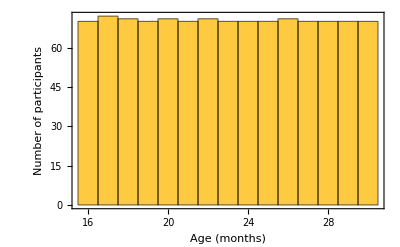

```mathematica
(*CDI被験者の月齢分布を示す．Show the age distribution of the CDI profiles.*)ageHistogram=Histogram[ageMonths,Frame->True,FrameLabel->{"Age (months)","Number of participants"},FrameStyle->14]
```

#### 総語彙数によるCDIデータと潜在座標の並べ替え Ordering CDI profiles and latent coordinates by total vocabulary size

```mathematica
(*各被験者の総語彙数．Total vocabulary size for each participant.*)
vocabularyTotals=Total/@alldata[[2;;,5;;]];

(*従来と同じ比較方法で，総語彙数による参加者順を求める．Determine participant order by vocabulary size using the same comparison as the original code.*)
vocabularyOrder=Sort[Transpose[{Range[Length[vocabularyTotals]],vocabularyTotals}],#1[[2]]<#2[[2]]&][[All,1]];

(*CDIデータを同じ順に並べ，見出し行を先頭に置く．Reorder CDI data and retain the header as the first row.*)
alldatasort=Prepend[alldata[[1+vocabularyOrder]],First[alldata]];

(*潜在平均と対数分散を同じ参加者順に並べる．Reorder latent means and log variances in the same order.*)
zdataEsort=zdataE[[vocabularyOrder]];
lσdataEsort=lσdata[[vocabularyOrder]];

(*後続の旧セルで使う名前を維持する．Retain the names used in later cells.*)
zdatasort=zdataEsort;
lσdatasort=lσdataEsort;

(*並べ替え後の総語彙数．Total vocabulary sizes in participant order.*)
totlist=vocabularyTotals[[vocabularyOrder]];

(*{順位，z1，z2，z3} の表．Table of {rank,z1,z2,z3}.*)
zdataswn=Transpose[Join[{Range[Length[zdatasort]]},Transpose[zdatasort]]];

(*{総語彙数，z1，z2，z3} の表．Table of {total vocabulary size,z1,z2,z3}.*)
totzdatasort=Transpose[Join[{totlist},Transpose[zdatasort]]];
```

#### 総語彙数の順位別表示と分布 Total vocabulary size by rank and its distribution

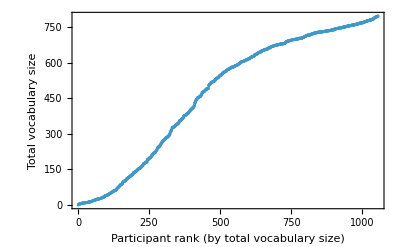

```mathematica
ListPlot[totlist,Frame->True,FrameLabel->{"Participant rank (by total vocabulary size)","Total vocabulary size"},FrameStyle->14]
```

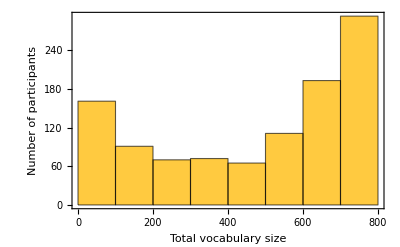

```mathematica
Histogram[totlist,Frame->True,FrameLabel->{"Total vocabulary size","Number of participants"},FrameStyle->14]
```

#### Encoder事後分布の不確実性 Uncertainty of the encoder posterior distributions

```mathematica
(*CDIプロフィールの潜在平均と，各次元の事後標準偏差を Around で表す．Represent a CDI profile by its latent mean and posterior standard deviation in each dimension using Around.*)ardata[x_]:=MapThread[Around,{toz[x],Exp[0.5 tologsigma[x]]}];
```

```mathematica
(*全語未獲得・全語獲得プロフィールの潜在位置と事後標準偏差．Latent positions and posterior standard deviations for the all-zero and all-one CDI profiles.*)zAllZero=toz[ConstantArray[0,d]];
zAllOne=toz[ConstantArray[1,d]];
arzzero=ardata[ConstantArray[0,d]];
arzall=ardata[ConstantArray[1,d]];
```

```mathematica
(*総語彙数順に並べたデータから，発達段階の異なる８名を選ぶ．Select eight children at different developmental stages from the data ordered by total vocabulary size.*)posteriorExampleRanks={20,101,287,381,515,601,704,1000};
posteriorExampleProfiles=Join[{ConstantArray[0,d],ConstantArray[1,d]},alldatasort[[posteriorExampleRanks+1,5;;]]];

posteriorExamples=ardata/@posteriorExampleProfiles;
```

```mathematica
pz2=latentSpaceReferencePlot=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.005],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[zAllZero]}],
Graphics3D[{Red,PointSize[0.03],Point[zAllOne]}]
]
```

-Graphics3D-

```mathematica
(*点は事後平均，誤差線は各潜在次元の±1 標準偏差を表す．Points indicate posterior means;error bars indicate±1 standard deviation in each latent dimension.*)posteriorUncertaintyPlot=Show[latentSpaceReferencePlot,ListPointPlot3D[posteriorExamples,PlotStyle->{{PointSize[0.01],Thickness[0.003],Red}}],ImageSize->500]
```

-Graphics3D-

#### 総語彙数順位ごとの潜在空間表示 Latent-space visualization by total vocabulary rank

```mathematica
pzt=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.006],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2},PlotLabel->Style["total vocabulary size (ascending order)",16]],
Graphics3D[{PointSize[0.03],Point[zAllZero]}],
Graphics3D[{Red,PointSize[0.03],Point[zAllOne]}]
]
```

-Graphics3D-

```mathematica
(*総語彙数順位380～390の11名を強調し，順位と総語彙数の範囲を示す．
Highlight the 11 children ranked 380–390 and annotate their rank and total-vocabulary-size ranges.*)
no1=380;no2=no1+10;
voc1=totlist[[no1]];
voc2=totlist[[no2]];
Show[pzt,ListPointPlot3D[zdatasort[[no1;;no2]],AspectRatio->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->{Magenta,PointSize[0.018]}],Graphics3D[Text[TextGrid[{{Style["ranking",14],Style[no1,14],Style["~",14],Style[no2,14]}}],{5,3,-3.5}]],
Graphics3D[Text[TextGrid[{{Style["voc",14],Style[voc1,14],Style["~",14],Style[voc2,14]}}],{5,3,-5}]]]
```

-Graphics3D-

```mathematica
(*総語彙数順に10名ずつ強調した動画フレームを作る．最後のフレームには残り６名を含める．Generate frames highlighting groups of 10 children in ascending total-vocabulary order.The final frame includes the remaining six.*)
mv1=Table[no1=k;
no2=Min[no1+9,Length[zdatasort]];
voc1=totlist[[no1]];
voc2=totlist[[no2]];
Show[pzt,ListPointPlot3D[zdatasort[[no1;;no2]],AspectRatio->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->{Magenta,PointSize[0.018]}],Graphics3D[Text[TextGrid[{{Style["ranking",14],Style[no1,14],Style["~",14],Style[no2,14]}}],{5,3,-3.5}]],Graphics3D[Text[TextGrid[{{Style["voc",14],Style[voc1,14],Style["~",14],Style[voc2,14]}}],{5,3,-5}]]],{k,1,Length[zdataEsort],10}];
```

```mathematica
mvout=ListAnimate[mv1]
```

#### 総語彙数順の移動窓平均による平均発達軌道 Mean developmental trajectory from moving-window averages in total-vocabulary order

```mathematica
nz=100;dnz=20;
```

```mathematica
meanzdata=Mean[#]&/@Partition[zdatasort,nz,dnz];
```

```mathematica
(*100名ずつの潜在平均点を，さらに５点の移動平均で平滑化して緑で示す．Show in green the five-point moving average of latent means computed from successive 100-child windows.*)baseplot2=Show[ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2},ImageSize->500],
Graphics3D[{PointSize[0.03],Point[zAllZero]}],
Graphics3D[{Red,PointSize[0.03],Point[zAllOne]}],
ListPointPlot3D[MovingAverage[meanzdata,5],AspectRatio->1,PlotStyle->{Green,PointSize[0.01]}]
]
```

-Graphics3D-

#### 総語彙数で着色した潜在空間（論文 Fig. 4a） Latent space colored by total vocabulary size (Fig. 4a)

```mathematica
(*総語彙数順に並べた各被験者の獲得語数と，799項目に対する割合．Total vocabulary size of each participant in vocabulary order and its proportion of the 799 CDI items.*)vocabSize=totlist;
vocabScore=Rescale[vocabSize,{0,799},{0,1}];
```

```mathematica
hexColor[s_String]:=RGBColor@@(FromDigits[#,16]&/@StringPartition[StringDrop[s,1],2]/255.)
```

```mathematica
(*総語彙数割合0，0.5，1に対応する紫の配色．明色は，基準色を中心に暗色と対称となる値を用いる．Purple palette for vocabulary proportions 0,0.5,and 1. The light color is symmetric to the dark color around the base color.*)lightPurple=RGBColor[40/51,188/255,329/255];
basePurple=hexColor["#7B6FD0"];
darkPurple=hexColor["#2E2257"];

{lightPurple,basePurple,darkPurple}
```

{RGBColor[Rational[40, 51], Rational[188, 255], Rational[329, 255]],RGBColor[0.4823529411764706, 0.43529411764705883, 0.8156862745098039],RGBColor[0.1803921568627451, 0.13333333333333333, 0.3411764705882353]}

```mathematica
vocabColor[x_]:=Blend[{{1.0,darkPurple},{0.5,basePurple},{0.0,lightPurple}},Clip[x,{0,1}]];
```

```mathematica
pointGraphics=Graphics3D[{PointSize[0.007],MapThread[{vocabColor[#2],Point[#1]}&,{zdatasort,vocabScore}]}];
```

```mathematica
legend=BarLegend[{vocabColor,{0,1}},LegendLabel->Style["Total vocabulary size",16],Ticks->{{0.0,"0.0"},{0.2,"0.2  (160 w)"},{0.4,"0.4  (320 w)"},{0.6,"0.6  (479 w)"},{0.8,"0.8  (639 w)"},{1.0,"1.0  (799 w)"}},LabelStyle->Directive[Black,14],LegendMarkerSize->140];

(* =====5. 描画=====*)phagi=Legended[Show[pointGraphics,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},Axes->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{2.0,-0.2,1.5},ImageSize->500],Placed[legend,Right]]
```

-Graphics3D-

#### 総語彙数で着色した潜在空間と４つの等総語彙割合面（論文 Fig. 4b） Latent space colored by total vocabulary size with four isosurfaces (Fig. 4b)

```mathematica
cnt02=ListContourPlot3D[gridall,Contours->{0.2},ContourStyle->Directive[vocabColor[0.2],Opacity[0.2]],Mesh->None,AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-6,6},{-6,6},{-6,6}}];
```

```mathematica
Show[phagi,cnt02];
```

```mathematica
(* =====等高面レベル. Isosurface levels=====*)
levels={0.2,0.4,0.6,0.8};
levelColors=vocabColor/@levels;
surfaceStyles=Directive[#,Opacity[0.3]]&/@levelColors;
```

```mathematica
(*４つの等総語彙割合面．Four isosurfaces of total vocabulary proportion.*)cntLevels=ListContourPlot3D[gridall,Contours->levels,ContourStyle->surfaceStyles,Mesh->None,PlotRange->{{-6,6},{-6,6},{-6,6}},BoxRatios->1,Axes->True,Boxed->True,Lighting->"Neutral"];
```

```mathematica
(*４つの等総語彙割合面．Four isosurfaces of total vocabulary proportion.*)surfaceLegend=SwatchLegend[levelColors,levels,LegendLabel->Style["Total vocabulary proportion",16],LabelStyle->Directive[Black,14],LegendMarkerSize->{22,14}];
```

```mathematica
(* =====散布図+等高面+凡例. Scatter plot,isosurfaces,and legend=====*)figContour3=Legended[Show[pointGraphics,cntLevels,PlotRange->{{-6,6},{-6,6},{-6,6}},BoxRatios->1,Axes->True,Boxed->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{2.0,-0.2,1.5},ImageSize->600],Placed[surfaceLegend,Right]];

figContour3
```

-Graphics3D-

#### Fig. 4cのための局所発達座標系の構築 Construction of the local developmental coordinate system for Fig. 4c

```mathematica
{nz,dnz}
```

{100,20}

```mathematica
zp=Partition[zdatasort,nz,dnz];
```

```mathematica
Length[zp]
```

48

```mathematica
k=10;Show[esys=Eigensystem[Covariance[zp[[k]]]];
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
ListPointPlot3D[zp[[k]],AspectRatio->1,PlotStyle->{Green,PointSize[0.006]}],
ListPointPlot3D[{Mean[zp[[k]]]},PlotStyle->{{PointSize[0.015],Black}}],
ListPointPlot3D[{Mean[zp[[k]]]+esys[[1,1]]^0.5esys[[2,1]]},PlotStyle->{PointSize[0.015],Orange}],
ListPointPlot3D[{Mean[zp[[k]]]+esys[[1,2]]^0.5esys[[2,2]]},PlotStyle->{PointSize[0.015],Magenta}]
,ImageSize->400
]
```

-Graphics3D-

```mathematica
(*全0・全1のCDIプロフィールの潜在座標の中点を，外向き方向を定める基準点とする．Use the midpoint between the latent positions of the all-zero and all-one CDI profiles as the reference point for the outward direction.*)center=0.5(toz[Table[0,d]]+toz[Table[1,d]])
```

{0.611139,0.911361,0.934436}

```mathematica
(*ベクトル列の各座標を平滑化する．meanfiltervecandend は両端に弱く平滑化した点を m 個ずつ追加する．Smooth each coordinate of a vector sequence.meanfiltervecandend adds m weakly smoothed points at each end.*)
```

```mathematica
meanfiltervec[vec_,n_]:=Module[{d,work,k},
d = Length[Transpose[vec]];
work= Table[MeanFilter[vec[[All,k]],n],{k,1,d}];
Transpose[work]
]
```

```mathematica
meanfiltervecandend[vec_,n_,m_]:=Module[{d,work,work2,trw,trw2,k},
d = Length[Transpose[vec]];
work2= Table[MeanFilter[vec[[All,k]],2],{k,1,d}];
work= Table[MeanFilter[vec[[All,k]],n],{k,1,d}];
trw2= Transpose[work2];
trw=Transpose[work];
Join[trw2[[1;;m]],trw,trw2[[-m;;-1]]]
]
```

```mathematica
tmp=Append[Mean[#]&/@zp,toz[Table[1,d]]];
```

```mathematica
tmp2 = meanfiltervec[tmp,5];
```

```mathematica
growdirection=Normalize[#]&/@Differences[tmp2];
```

```mathematica
outdirection= Normalize[(# - center)]&/@meanzdata;
```

```mathematica
leftdirection=Table[Normalize[Cross[growdirection[[k]],outdirection[[k]]]],{k,1,Length[zp]}];
```

```mathematica
k=1;Show[
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.0045],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Thickness[0.004],Arrow[{meanzdata[[k]],meanzdata[[k]]+1.5growdirection[[k]]}]}],Graphics3D[{Red,Thickness[0.004],Arrow[{meanzdata[[k]],meanzdata[[k]]+1.5outdirection[[k]]}]}],Graphics3D[{Green,Thickness[0.004],Arrow[{meanzdata[[k]],meanzdata[[k]]+1.5leftdirection[[k]]}]}],ImageSize->500
]
```

-Graphics3D-

```mathematica
esyss=Table[Eigensystem[Covariance[zp[[k]]]],{k,1,Length[zp]}];
```

```mathematica
(*３つの局所主成分から参照方向との内積の絶対値が最大のものを選び，主成分番号と向きの符号を返す．Select the local principal component with the largest absolute dot product with the reference direction,and return its index and orientation sign.*)
```

```mathematica
whichvec[vec_,ref_]:=Module[{work,work2},
work=(ref.#)&/@vec;
work2=Sort[Transpose[{Range[Length[work]],work}],Abs[#1[[2]]]>Abs[#2[[2]]]&];
{work2[[1,1]],Sign[work2[[1,2]]]}
]
```

```mathematica
out=Table[whichvec[esyss[[k,2]],outdirection[[k]]],{k,1,Length[zp]}]
```

{{2,-1},{2,-1},{3,-1},{3,1},{3,1},{3,-1},{3,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{2,-1},{3,1},{3,1},{3,1},{3,1},{3,1},{3,1},{3,1},{3,1},{3,1},{3,1}}

```mathematica
leftv=Table[whichvec[esyss[[k,2]],leftdirection[[k]]],{k,1,Length[zp]}]
```

{{2,1},{2,1},{2,1},{2,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,-1},{1,-1}}

最初の２窓では Out と Left がともに第２主成分を選ぶため，Left を第３主成分の負方向に指定する．
 In the first two windows, Out and Left both select the second principal component, so assign Left to the negative third principal component .

```mathematica
leftv[[1]]={3,-1}
```

{3,-1}

```mathematica
leftv[[2]]={3,-1}
```

{3,-1}

```mathematica
(*最初の局所窓で Out と Left の２標準偏差位置を計算し，２方向の直交性と潜在空間での向きを確認する．
For the first local window,compute the 2-SD positions in the Out and Left directions,then check their orthogonality and orientation in latent space.*)
```

```mathematica
k=20;outer2work=meanzdata[[k]]+2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]]
left2work=meanzdata[[k]]+2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]]
```

{-2.91833,-1.29319,0.264084}

{-0.285033,-4.29912,1.97739}

```mathematica
(outer2work-meanzdata[[k]]).(left2work-meanzdata[[k]])
```

-2.22045×10^-16

```mathematica
k=20;
outer2work=meanzdata[[k]]+2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]];
left2work=meanzdata[[k]]+2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]];
Show[
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.0035],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Red,Thickness[0.004],Arrow[{meanzdata[[k]],outer2work}]}],Graphics3D[{Green,Thickness[0.004],Arrow[{meanzdata[[k]],left2work}]}],ImageSize->400,ViewPoint->{1,-3,4}
]
```

-Graphics3D-

```mathematica
(*各局所窓の平均から，Out–In と Left–Right の方向に±2 標準偏差離れた点を求める．For each local window,compute points at±2 SD along the Out–In and Left–Right directions from its mean.*)
```

```mathematica
outer2 = Table[meanzdata[[k]]+2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
inner2 = Table[meanzdata[[k]]-2out[[k,2]]esyss[[k,1,out[[k,1]]]]^0.5 esyss[[k,2,out[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
left2=Table[meanzdata[[k]]+2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
right2=Table[meanzdata[[k]]-2leftv[[k,2]]esyss[[k,1,leftv[[k,1]]]]^0.5 esyss[[k,2,leftv[[k,1]]]],{k,1,Length[zp]}];
```

```mathematica
nfilter=10;
pdev=Show[
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.0045],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-0.5,0.}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Blue,PointSize[0.01],Point[Mean[zp[[43]]]]}],
ListPointPlot3D[meanfiltervecandend[meanzdata,nfilter,4],AspectRatio->1,PlotStyle->Green],
ListPointPlot3D[meanfiltervecandend[outer2,nfilter,4],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervecandend[inner2,nfilter,4],AspectRatio->1,PlotStyle->Orange],
ListPointPlot3D[meanfiltervecandend[left2,nfilter,4],AspectRatio->1,PlotStyle->Magenta],ListPointPlot3D[meanfiltervecandend[right2,nfilter,4],AspectRatio->1,PlotStyle->Magenta],ImageSize->500
]
```

-Graphics3D-

#### 総語彙数で着色した潜在空間と５本の発達軌道（論文 Fig. 4c） Latent space colored by total vocabulary size with five developmental trajectories (Fig. 4c)

```mathematica
(*５本の軌道の色を定義し，Left，Right，Center，Out，In の順に表示する．Define colors for the five trajectories and display them in Left,Right,Center,Out,and In order.*)
```

```mathematica
leftc=hexColor["#2C7BB6"];centerc=hexColor["#7B6FD0"];rightc=hexColor["#1A9850"];outc=hexColor["#E8A93E"];
inc=hexColor["#D86F93"];
{leftc,rightc,centerc,outc,inc}
```

{RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.10196078431372549, 0.596078431372549, 0.3137254901960784],RGBColor[0.4823529411764706, 0.43529411764705883, 0.8156862745098039],RGBColor[0.9098039215686274, 0.6627450980392157, 0.24313725490196078],RGBColor[0.8470588235294118, 0.43529411764705883, 0.5764705882352941]}

```mathematica
pointGraphics2=Graphics3D[{PointSize[0.0065],MapThread[{vocabColor[#2],Point[#1]}&,{zdatasort,vocabScore}]}];
```

```mathematica
phagi2=Show[pointGraphics2,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},Axes->True,AxesLabel->{Style["z1",20,GrayLevel[0.15]],Style["z2",20,GrayLevel[0.15]],Style["z3",20,GrayLevel[0.15]]},TicksStyle->Directive[GrayLevel[0.2],14],AxesStyle->Directive[GrayLevel[0.2],15],BoxStyle->GrayLevel[0.4],ViewPoint->{2.0,0.1,1.},ImageSize->500];
```

```mathematica
nfilter=10;
Show[phagi2,ListPointPlot3D[meanfiltervecandend[meanzdata,nfilter,6],AspectRatio->1,PlotStyle->centerc],ListPointPlot3D[meanfiltervecandend[outer2,nfilter,6],AspectRatio->1,PlotStyle->outc],ListPointPlot3D[meanfiltervecandend[inner2,nfilter,6],AspectRatio->1,PlotStyle->inc],ListPointPlot3D[meanfiltervecandend[left2,nfilter,6],AspectRatio->1,PlotStyle->leftc],ListPointPlot3D[meanfiltervecandend[right2,nfilter,6],AspectRatio->1,PlotStyle->rightc],ImageSize->500]
```

-Graphics3D-

#### 局所PCAの±2σ変位に基づく楕円チューブ Elliptical tube based on ±2 SD displacements from local PCA

```mathematica
nfilter=10;
```

```mathematica
meanzMF=meanfiltervecandend[meanzdata,nfilter,4];
outerMF=meanfiltervecandend[outer2,nfilter,4];
rightMF =meanfiltervecandend[right2,nfilter,4];
```

```mathematica
out2vec = outerMF-meanzMF;
```

```mathematica
right2vec= rightMF - meanzMF;
```

```mathematica
(*平滑化した中心軌道の各点で，Right と Out への変位を使って楕円断面を作る．At each point on the smoothed center trajectory,form an elliptical cross-section using the displacements toward Right and Out.*)
test=Table[Table[meanzMF[[k]]+right2vec[[k]]Cos[α]+out2vec[[k]]Sin[α],{α,0,2Pi,2Pi/40}],{k,1,Length[meanzMF]}];
```

```mathematica
s1=Show[
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.006],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2.0,-0.2,1.5}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
ListPointPlot3D[meanzMF,AspectRatio->1,PlotStyle->Green],
ListPointPlot3D[Flatten[test,1],PlotStyle->{Magenta,PointSize[0.005]}],ImageSize->500
]
```

-Graphics3D-

#### 楕円断面の点列とチューブ面の確認 Inspecting elliptical cross-sections and the tube surface

```mathematica
Show[phagi2,ListPointPlot3D[meanzMF,AspectRatio->1,PlotStyle->centerc],ListPointPlot3D[Flatten[test,1],PlotStyle->{Green,PointSize[0.005]}],ImageSize->500]
```

-Graphics3D-

```mathematica
ss=GradientFittedMesh[Flatten[test,1]];
```

```mathematica
ss1=Graphics3D[{Opacity[0.3],ss}]
```

-Graphics3D-

```mathematica
Show[s1,ss1]
```

-Graphics3D-

```mathematica
(*局所共分散の３つの固有値と，選択した Out–In・Left–Right 方向の標準偏差を表示する．Plot the three eigenvalues of each local covariance matrix and the SDs along the selected Out–In and Left–Right directions.*)
```

```mathematica
evlist=Transpose[esyss[[All,1]]];
```

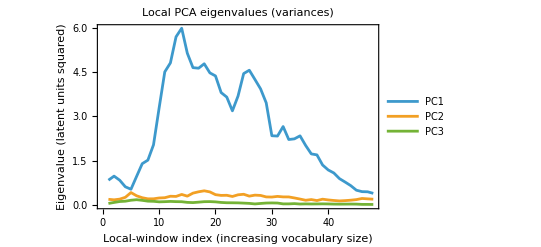

```mathematica
ListLinePlot[evlist,Frame->True,FrameLabel->{Style["Local-window index (increasing vocabulary size)",14],Style["Eigenvalue (latent units squared)",14]},PlotLabel->Style["Local PCA eigenvalues (variances)",16],PlotLegends->Placed[{"PC1","PC2","PC3"},Right],ImageSize->400]
```

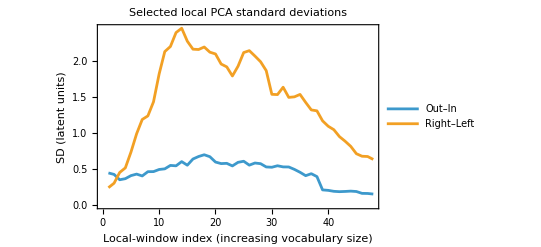

```mathematica
ListLinePlot[Transpose[Table[{esyss[[k,1,out[[k,1]]]]^0.5,esyss[[k,1,leftv[[k,1]]]]^0.5},{k,1,Length[zp]}]],Frame->True,FrameLabel->{Style["Local-window index (increasing vocabulary size)",14],Style["SD (latent units)",14]},PlotLabel->Style["Selected local PCA standard deviations",16],PlotLegends->Placed[{"Out–In","Right–Left"},Right],ImageSize->400]
```

#### 潜在空間グリッド上の Decoder 出力と補間関数 Decoder outputs on the latent-space grid and their interpolation functions

```mathematica
(*後続の補間関数の入力を明示するため，grid，decall，gridall をここで再計算する．
Recompute grid,decall,and gridall here to show the inputs used by the interpolation functions below.*)
```

```mathematica
grid=Table[revm.{i,j,k},{i,-6,6,12/29//N},{j,6,-6,-12/29//N},{k,6,-6,-12/29//N}];
```

```mathematica
decall=decallorg;
```

```mathematica
gridall=Flatten[Table[{grid[[i,j,k]],Mean[decall[[;;,i,j,k]]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
```

```mathematica
(*先に作成した gridall を補間し，潜在座標から総語彙割合を求める関数 fall を定義する．Interpolate the previously constructed gridall to define fall,which maps latent coordinates to total vocabulary proportion.*)
```

```mathematica
fall=Interpolation[gridall];
```

```mathematica
{fall[0,0,0],Mean[predict[{0,0,0}]]}
```

{0.502587,0.501993}

```mathematica
(*grid data isodurface*)
```

```mathematica
(*  tmp=Flatten[Table[{grid[[i,j,k]],decall[[700,i,j,k]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
ListContourPlot3D[tmp,Contours->0.5,ContourStyle->{cl[[2]],Opacity[0.2]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotRange->{{-6,6},{-6,6},{-6,6}}]*)
```

#### 語別 Decoder 出力の補間関数 fitem：作成手順と読み込み Itemwise decoder interpolation functions fitem: construction and loading

```mathematica
(*各語のグリッド上の Decoder 出力から fitem を作成した手順を記録する．保存済みの関数は下の Get で読み込む．Record how the word-specific interpolants fitem were constructed from decoder outputs on the grid.Load the saved functions below with Get.*)
```

```mathematica
(* For[kitem=1,kitem<800,kitem++,
tmp=Flatten[Table[{grid[[i,j,k]],decall[[kitem,i,j,k]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
tmp2 = {{#[[1]],#[[2]],#[[3]]},#[[4]]}&/@tmp;
fitem[kitem]=Interpolation[tmp2];]*)
```

```mathematica
(*Save[FileNameJoin[{dirw,"fitem-mand-3D-reversed"}],fitem];*)
```

```mathematica
Get[FileNameJoin[{dirw,"fitem-mand-3D-reversed"}]];
```

```mathematica
(*第799語について，同じ潜在座標で fitem の補間値と Decoder の直接出力を比較する．Compare the interpolated fitem value with the direct decoder output for item 799 at the same latent position.*)
```

```mathematica
fitem[799][3,3,3]
```

0.78926

```mathematica
predict[{3,3,3}][[799]]
```

0.789318

```mathematica
(*CDI kitem番目の語彙の補間された表出確率が itemProbLevel となる等値面を，CDIプロフィールの潜在座標とともに表示する．Display the itemProbLevel isosurface of the interpolated production probability for item (kitem-th) together with the CDI latent positions.*)
```

```mathematica
kitem=1;fitem4[kitem]
```

{1,a-sounds,喂？,a1,hello}

```mathematica
kitem=1;
itemProbLevel=0.4;

Show[
ListPointPlot3D[zdatasort,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.005],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotLabel->fitem3[kitem],ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
(* ParametricPlot3D[{devcenter2f[[1]][t],devcenter2f[[2]][t],devcenter2f[[3]][t]},{t,1,95},PlotStyle->Green],*)ContourPlot3D[fitem[kitem][x,y,z]==itemProbLevel,{x,-6,6},{y,-6,6},{z,-6,6},ContourStyle->{cl[[2]],Opacity[0.2]},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},PlotLabel->fitem4[kitem],PlotRange->{{-6,6},{-6,6},{-6,6}}]]
```

-Graphics3D-

```mathematica
(*局所PCAの±2σ変位に基づく楕円チューブと，総語彙割合が vocabProportionLevel となる等値面を重ね，潜在空間での位置関係を確認する．Overlay the elliptical tube based on±2 SD displacements from local PCA with the isosurface where total vocabulary proportion equals vocabProportionLevel,and inspect their spatial relationship in latent space.*)
```

```mathematica
vocabProportionLevel=0.1;

Show[s1,ss1,ContourPlot3D[fall[x,y,z]==vocabProportionLevel,{x,-6,6},{y,-6,6},{z,-6,6},ContourStyle->{cl[[2]],Opacity[0.2]}]]
```

-Graphics3D-

#### 平均発達軌道の平滑化と終点の追加 Smoothing the mean developmental trajectory and adding its endpoint

```mathematica
nfilter=10;
```

```mathematica
meanzMF=meanfiltervecandend[meanzdata,nfilter,4];
```

```mathematica
(*中国語では低語彙割合側の軌道が曲がるため，ここでは全０プロフィールの潜在座標を加えず，全１プロフィールの潜在座標を終点に加える．For Mandarin,the trajectory bends at low vocabulary proportions.Here we append the latent position of the all-one profile as the endpoint and leave the lower end for the extrapolation below.*)
```

```mathematica
meanzMF2= Join[meanzMF,{toz[Table[1,d]]}];
```

```mathematica
(*軌道上の各点で Decoder 出力の799項目平均を求め，総語彙割合の指標とする．
At each trajectory point,compute the mean decoder output over 799 items as the total vocabulary proportion.*)
```

```mathematica
voadevcenter2=Mean[predict[#]]&/@meanzMF2;
```

```mathematica
(*最初の２点の潜在座標と総語彙割合の関係を線形外挿し，外挿値が０となる潜在座標 Xzero を求める．Linearly extrapolate the relation between latent position and total vocabulary proportion from the first two points to obtain Xzero,where the extrapolated proportion is zero.*)
```

```mathematica
ΔX = meanzMF2[[2]]-meanzMF2[[1]];
```

```mathematica
Δvoa = voadevcenter2[[2]] - voadevcenter2[[1]];
```

```mathematica
Xzero = -ΔX/Δvoa voadevcenter2[[1]]+ meanzMF2[[1]]
```

{2.19573,-1.71655,-5.03615}

```mathematica
Total[predict[Xzero]]
```

12.8343

```mathematica
fall[Xzero[[1]],Xzero[[2]],Xzero[[3]]]
```

0.0160622

```mathematica
(*外挿点 Xzero を平均軌道の先頭に加える．
Prepend the extrapolated point Xzero to the mean trajectory.
*)
```

```mathematica
meanzMF2zero = Join[{Xzero},meanzMF2];
```

```mathematica
(*Xzero を加える前の平均軌道について，3つの潜在座標を点番号の関数として補間する．Interpolate the three latent coordinates of the mean trajectory before adding Xzero as functions of the point index.*)
```

```mathematica
devcenter2f=Table[Interpolation[meanzMF2[[All,k]]],{k,1,3,1}];
```

```mathematica
(*折れ線で Xzero と平均軌道を結び，緑の曲線で meanzMF2 の補間を示す．
The polyline connects Xzero to the mean trajectory;the green curve shows the interpolation of meanzMF2.*)
```

```mathematica
pdevtmp=Show[
ListPointPlot3D[zdataE,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},PlotStyle->PointSize[0.005],AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{2,-3,2}],
Graphics3D[{PointSize[0.03],Point[toz[Table[0,d]]]}],
Graphics3D[{Red,PointSize[0.03],Point[toz[Table[1,d]]]}],
Graphics3D[{Blue,PointSize[0.03],Point[Xzero]}],
 ListLinePlot3D[meanzMF2zero,PlotStyle->Thickness[0.0035]],
ParametricPlot3D[{devcenter2f[[1]][t],devcenter2f[[2]][t],devcenter2f[[3]][t]},{t,1,Length[meanzMF2]},PlotStyle->Green]
]
```

-Graphics3D-

#### ５本の発達軌道の平滑化と端点の確認 Smoothing the five developmental trajectories and checking their endpoints

```mathematica
meanzMF=meanfiltervecandend[meanzdata,nfilter,4];
outerMF=meanfiltervecandend[outer2,nfilter,4];
innerMF=meanfiltervecandend[inner2,nfilter,4];
rightMF =meanfiltervecandend[right2,nfilter,4];
leftMF =meanfiltervecandend[left2,nfilter,4];
```

```mathematica
(*全0・全1プロフィールの潜在点，Xzero，および５本の軌道の端点で，Decoder が推定する総語彙割合を比較する．Compare decoder-predicted total vocabulary proportions at the all-zero and all-one latent points,Xzero,and the endpoints of the five trajectories.*)
```

```mathematica
<|"AllZero"->Mean[predict[toz[ConstantArray[0,d]]]],"Xzero"->Mean[predict[Xzero]],"Center"->Mean[predict[First[meanzMF]]],"Out"->Mean[predict[First[outerMF]]],"In"->Mean[predict[First[innerMF]]],"Left"->Mean[predict[First[leftMF]]],"Right"->Mean[predict[First[rightMF]]]|>
```

<|AllZero→0.0798961,Xzero→0.016063,Center→0.0331506,Out→0.0328867,In→0.0354485,Left→0.0339154,Right→0.0333704|>

```mathematica
<|"AllOne"->Mean[predict[toz[ConstantArray[1,d]]]],"Center"->Mean[predict[Last[meanzMF]]],"Out"->Mean[predict[Last[outerMF]]],"In"->Mean[predict[Last[innerMF]]],"Left"->Mean[predict[Last[leftMF]]],"Right"->Mean[predict[Last[rightMF]]]|>
```

<|AllOne→0.963855,Center→0.936701,Out→0.942018,In→0.929868,Left→0.911028,Right→0.943117|>

```mathematica
(*Xzero から５本の軌道の始点へ，また各終点から全1プロフィールの潜在点へ つなぐ区間の総語彙割合を確認する．Check total vocabulary proportions along the connections from Xzero to the five trajectory starts and from their ends to the all-one latent point.*)
```

```mathematica
seq[ini_,fin_,ndiv_]:= Module[{delta},
delta = (fin -ini)/ndiv;
Table[ini + delta (k-1),{k,1,ndiv+1}]
]
```

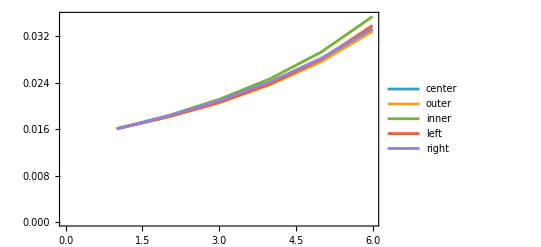

```mathematica
ListLinePlot[{
fall[#[[1]],#[[2]],#[[3]]]&/@seq[Xzero,meanzMF[[1]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[Xzero,outerMF[[1]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[Xzero,innerMF[[1]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[Xzero,leftMF[[1]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[Xzero,rightMF[[1]],5]
},PlotLegends->{"center","outer","inner","left","right"},Frame->True]
```

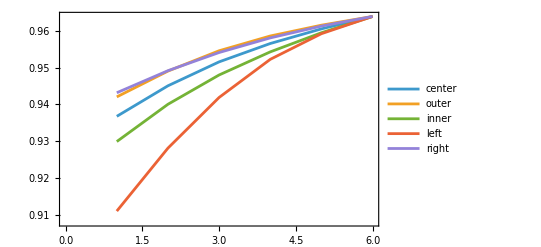

```mathematica
ListLinePlot[{
fall[#[[1]],#[[2]],#[[3]]]&/@seq[meanzMF[[-1]],toz[Table[1,d]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[outerMF[[-1]],toz[Table[1,d]],5],fall[#[[1]],#[[2]],#[[3]]]&/@seq[innerMF[[-1]],toz[Table[1,d]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[leftMF[[-1]],toz[Table[1,d]],5],
fall[#[[1]],#[[2]],#[[3]]]&/@seq[rightMF[[-1]],toz[Table[1,d]],5]
},PlotLegends->{"center","outer","inner","left","right"},Frame->True]
```

```mathematica
meanzMF2=meanzMF;
outerMF2=outerMF;
innerMF2=innerMF;
rightMF2=rightMF;
leftMF2=leftMF;
```

```mathematica
(*平滑化した５本の軌道を Xzero と全1プロフィールの潜在点へ延長する．Extend the five smoothed trajectories to Xzero and the all-one latent point.*)extendTrajectoryToEndpoints[path_,zStart_,zEnd_,nSegments_:5]:=Join[Most[Subdivide[zStart,First[path],nSegments]],path,Rest[Subdivide[Last[path],zEnd,nSegments]]];

smoothedTrajectories=<|"Center"->meanzMF2,"Left"->leftMF2,"Right"->rightMF2,"In"->innerMF2,"Out"->outerMF2|>;
extendedTrajectories=Map[extendTrajectoryToEndpoints[#,Xzero,zAllOne,5]&,smoothedTrajectories];

(*後続コードで使う５本の端点付き軌道を定義する．Define the five endpoint-extended trajectories used below.*)meanzMF3=extendedTrajectories["Center"];
leftMF3=extendedTrajectories["Left"];
rightMF3=extendedTrajectories["Right"];
innerMF3=extendedTrajectories["In"];
outerMF3=extendedTrajectories["Out"];

Dimensions/@extendedTrajectories
```

<|Center→{66,3},Left→{66,3},Right→{66,3},In→{66,3},Out→{66,3}|>

```mathematica
(*軌道点を総語彙割合でパラメータ化する．Parameterize trajectory points by total vocabulary proportion.*)makeVocabularyTrajectory[points_]:=Module[{vocabProportion,coordinateFunctions,vocabProportionToIndex},vocabProportion=Mean[predict[#]]&/@points;
coordinateFunctions=Table[Interpolation[points[[All,k]],InterpolationOrder->1],{k,1,3}];
vocabProportionToIndex=Interpolation[Transpose[{vocabProportion,Range[Length[points]]}],InterpolationOrder->1];
<|"Points"->points,"VocabularyProportion"->vocabProportion,"CoordinateFunctions"->coordinateFunctions,"VocabularyProportionToIndex"->vocabProportionToIndex|>];

trajectoryPoint[trajectory_Association,ptot_]:=Through[trajectory["CoordinateFunctions"][trajectory["VocabularyProportionToIndex"][ptot]]];

vocabularyTrajectories=makeVocabularyTrajectory/@extendedTrajectories;

Dimensions[#["Points"]]&/@vocabularyTrajectories
```

<|Center→{66,3},Left→{66,3},Right→{66,3},In→{66,3},Out→{66,3}|>

```mathematica
voadevcenter3=vocabularyTrajectories["Center"]["VocabularyProportion"];
voadevleft3=vocabularyTrajectories["Left"]["VocabularyProportion"];
voadevright3=vocabularyTrajectories["Right"]["VocabularyProportion"];
voadevinner3=vocabularyTrajectories["In"]["VocabularyProportion"];
voadevouter3=vocabularyTrajectories["Out"]["VocabularyProportion"];

devcenter3f=vocabularyTrajectories["Center"]["CoordinateFunctions"];

zcenter3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Center"],ptot];
zleft3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Left"],ptot];
zright3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Right"],ptot];
zin3[ptot_]:=trajectoryPoint[vocabularyTrajectories["In"],ptot];
zout3[ptot_]:=trajectoryPoint[vocabularyTrajectories["Out"],ptot];
```

```mathematica
(*５本の軌道の点数，総語彙割合の単調性，両端を確認する．
Validate the point counts,increasing vocabulary proportions,and endpoints of the five trajectories.*)<|"PointCounts"->(Length/@extendedTrajectories),"StrictlyIncreasing"->(AllTrue[Differences[#["VocabularyProportion"]],Positive]&/@vocabularyTrajectories),"StartErrors"->(Max[Abs[First[#]-Xzero]]&/@extendedTrajectories),"EndErrors"->(Max[Abs[Last[#]-zAllOne]]&/@extendedTrajectories)|>
```

<|PointCounts→<|Center→66,Left→66,Right→66,In→66,Out→66|>,StrictlyIncreasing→<|Center→True,Left→True,Right→True,In→True,Out→True|>,StartErrors→<|Center→0.,Left→0.,Right→0.,In→0.,Out→0.|>,EndErrors→<|Center→0.,Left→0.,Right→0.,In→0.,Out→0.|>|>

#### 中央発達軌道に沿った各語のVoAと発達幅の推定・可視化 Estimation and visualization of word-level VoA and developmental width along the center trajectory

```mathematica
(*fitem の作成方法を記録する．現在は保存済みの fitem を読み込んで使用する．Record how fitem was constructed.The saved fitem functions are loaded for the current analysis.*)
```

```mathematica
(* For[kitem=1,kitem<800,kitem++,
tmp=Flatten[Table[{grid[[i,j,k]],decall[[kitem,i,j,k]]}//Flatten,{i,1,30},{j,1,30},{k,1,30}],2];
tmp2 = {{#[[1]],#[[2]],#[[3]]},#[[4]]}&/@tmp;
fitem[kitem]=Interpolation[tmp2];]*)
```

```mathematica
(*中央軌道上で799語それぞれの表出確率の曲線を作る．Xzero での予測総語彙数は約13語相当なので，各曲線に 仮想的な {t=0，表出確率=0} を追加する．Xzero は t=1 に対応し，t=0 に潜在空間上の点はない．Build a production-probability curve for each of the 799 words along the center trajectory.The predicted vocabulary size at Xzero is equivalent to about 13 words,so an artificial {t=0,production probability=0} is added to each curve.Xzero corresponds to t=1;there is no latent point at t=0.*)
centerPathPoints=extendedTrajectories["Center"];
centerPathIndex=Range[0,Length[centerPathPoints]];

centerWordValues=Table[fitem[k]@@@centerPathPoints,{k,1,d}];

centerWordValuesWithZero=Prepend[#,0]&/@centerWordValues;

centerWordCurves=(Interpolation[Transpose[{centerPathIndex,#}]]&)/@centerWordValuesWithZero;

Clear[fitemcenter];
fitemcenter[k_Integer]:=centerWordCurves[[k]];

(*各時点で799語の表出確率を平均し，総語彙割合の曲線を補間する．Average the 799 word probabilities at each index and interpolate the resulting total-vocabulary-proportion curve.*)
fallcenter=Interpolation[Transpose[{centerPathIndex,Mean/@Transpose[centerWordValuesWithZero]}]];
```

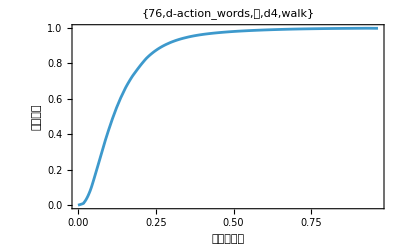

```mathematica
kitem=76;ParametricPlot[{fallcenter[t],fitemcenter[kitem][t]},{t,0,  Length[meanzMF3]},AspectRatio->1/GoldenRatio,PlotLabel->fitem4[kitem],Frame->True,FrameLabel->{"総語彙確率","表出確率"},FrameStyle->14,PlotRange->All]
```

```mathematica
(*英語版の pTot3 に対応する計算．中央軌道上で fitem[kitem] が指定確率に達する位置を求め，その位置の総語彙割合を fall から返す．Calculation corresponding to pTot3 in the English notebook.Find where fitem[kitem] reaches the specified probability along the center trajectory,then return the total vocabulary proportion from fall at that position.*)
pTot3[kitem_,perc_]:= fall[devcenter3f[[1]][t],devcenter3f[[2]][t],devcenter3f[[3]][t]]/.FindRoot[fitem[kitem][devcenter3f[[1]][t],devcenter3f[[2]][t],devcenter3f[[3]][t]]==perc,{t,1,  Length[meanzMF3]}]
```

```mathematica
(*中国語版の後続の VoA 計算で使用する方法．補間した fitemcenter[kitem] が指定確率に達する t を求め，fallcenter[t] を返す．Method used for the subsequent Mandarin VoA calculations.Find t where the interpolated fitemcenter[kitem] reaches the specified probability,then return fallcenter[t].*)pTotcenter[kitem_,perc_]:= fallcenter[t]/.FindRoot[fitemcenter[kitem][t]==perc,{t,0,  Length[meanzMF3]}]
```

```mathematica
pTot3[799,0.5]
```

0.941943

```mathematica
percentilelist= Table[{pTotcenter[ki,0.25],pTotcenter[ki,0.5],pTotcenter[ki,0.75]},{ki,1,799,1}];
```

InterpolatingFunction::dmval: 入力値{77.534}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{67.1534}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

```mathematica
(*50％の表出確率に達する総語彙割合を，各語の VoA とする．Use the total vocabulary proportion at 50% production probability as each word's VoA.*)wordVoA=percentilelist[[All,2]];

(*VoA と，75％点から25％点までの発達幅を組み合わせる．Combine each word's VoA with its developmental width between the 25% and 75% production thresholds.*)
voaSpreadData=Transpose[{wordVoA,percentilelist[[All,3]]-percentilelist[[All,1]]}];

(*後続の旧コードで使う名前を暫定的に維持する．Retain the name used by later code for now.*)
dp31=voaSpreadData;
```

#### VoAと発達幅の散布図：語情報のTooltipとカテゴリーの強調 Scatter plot of VoA and developmental width with word tooltips and highlighted categories

```mathematica
(*各点に語の情報を Tooltip として付ける．Attach word information to each point as a tooltip.*)voaSpreadWithTooltips=MapThread[Tooltip[#1,#2]&,{voaSpreadData,fitem4/@Range[Length[voaSpreadData]]}];

(*後続の旧コードで使う名前を暫定的に維持する．Retain the name used by later code for now.*)
ttdp31=voaSpreadWithTooltips;
```

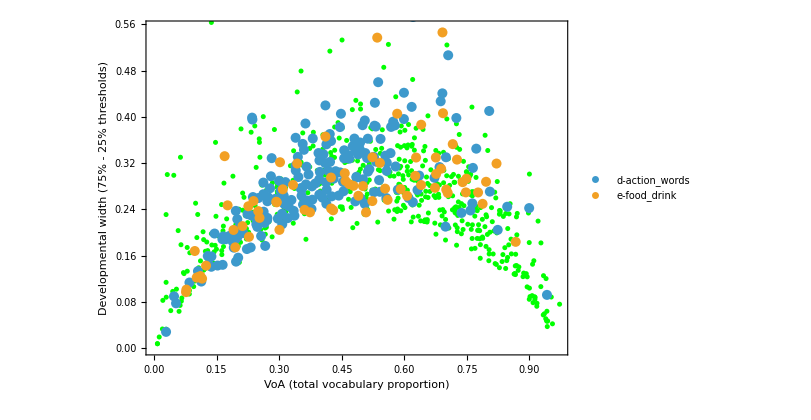

```mathematica
(*全語を表示し，カテゴリー4・5を強調する．Plot all words and highlight categories 4 and 5.*)
highlightedCategories={4,5};

highlightedVoAData=(voaSpreadWithTooltips[[#[[1]];;#[[2]]]]&)/@catns[[highlightedCategories]];

allWordsVoAPlot=ListPlot[voaSpreadWithTooltips,PlotStyle->{Green,PointSize[0.006]},AspectRatio->0.7,Frame->True,FrameStyle->16,FrameLabel->{"VoA (total vocabulary proportion)","Developmental width (75% - 25% thresholds)"},ImageSize->600];

highlightedCategoriesPlot=ListPlot[highlightedVoAData,Frame->True,PlotStyle->PointSize[0.012],PlotLegends->catname[[highlightedCategories]]];

Show[allWordsVoAPlot,highlightedCategoriesPlot]
```

### 24カテゴリー内での語のVoA順序付け Ordering words by VoA within the 24 categories

```mathematica
(*各項目の情報に，計算済みのVoAを追加する．Append the previously computed VoA to each item's information.*)itemsvoa0=MapThread[Append,{fitem4/@Range[Length[wordVoA]],wordVoA}];
```

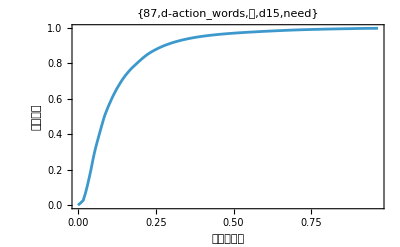

```mathematica
kitem=87;ParametricPlot[{fallcenter[t],fitemcenter[kitem][t]},{t,0,  Length[meanzMF3]},AspectRatio->1/GoldenRatio,PlotLabel->fitem4[kitem],Frame->True,FrameLabel->{"総語彙確率","表出確率"},FrameStyle->14,PlotRange->All]
```

```mathematica
(*24カテゴリーそれぞれの語をVoAの小さい順に並べる．Sort words within each of the 24 categories by increasing VoA.*)itemsByCategory=(itemsvoa0[[#[[1]];;#[[2]]]]&)/@catn;
sortedItemsByCategory=SortBy[#,Last]&/@itemsByCategory;

itemsvoa=Flatten[sortedItemsByCategory,1];
orderbyvoa=itemsvoa[[All,1]];
```

#### 総語彙割合 ptot からカテゴリー別 VoA 順の語順位置への変換 Mapping total vocabulary proportion (ptot) to word-rank position in category-wise VoA order

```mathematica
(*各語のVoAを節点として，総語彙割合ptotから カテゴリーを連結した語順位置への対応を作る．Use word VoA values as knots to map total vocabulary proportion ptot to word-rank position in the concatenated category ordering.*)ptotToRankDataForCategory[{firstItem_Integer,lastItem_Integer}]:=Join[{{0,firstItem-1}},Transpose[{itemsvoa[[firstItem;;lastItem,-1]],Range[firstItem,lastItem]}],{{1,lastItem+1}}];

ptotToRankData=ptotToRankDataForCategory/@catn;
ptotToRankFunctions=Interpolation[#,InterpolationOrder->1]&/@ptotToRankData;

Clear[ptotToRank,voa2n];
ptotToRank[nc_Integer]:=ptotToRankFunctions[[nc]];

(*後続セルで使う旧名を維持する．Keep the former name for subsequent cells.*)
voa2n[nc_Integer]:=ptotToRank[nc];
```

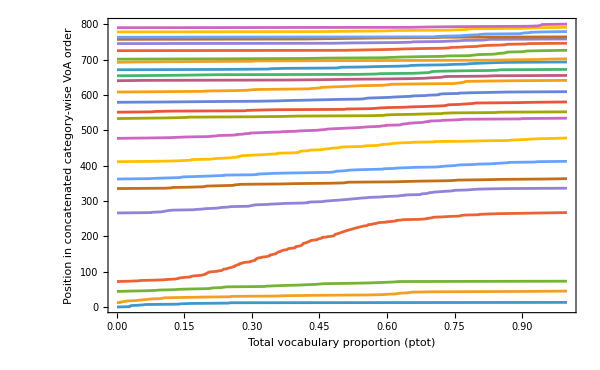

```mathematica
(*24カテゴリーについて，ptotに対応するVoA順の語順位置を描く．ptot=0，1は補間用の端点である．Plot the word-rank position corresponding to ptot for all 24 categories.The points at ptot=0 and 1 are interpolation anchors.*)Module[{p},Plot[Evaluate@Table[ptotToRank[nc][p],{nc,1,Length[catn]}],{p,0,1},Frame->True,FrameLabel->{"Total vocabulary proportion (ptot)","Position in concatenated category-wise VoA order"},PlotRange->All,ImageSize->600,FrameStyle->13]]
```

#### 潜在空間の中央発達軌道と総語彙割合0.5の等値面上の５点 Center developmental trajectory and five points on the ptot = 0.5 isosurface

```mathematica
(*CDIデータ，全0・全1プロファイル，中央発達軌道を表示する．Show the CDI data，the all-zero and all-one profiles，and the center developmental trajectory．*)pdevtmp=Show[latentSpaceReferencePlot,ParametricPlot3D[Evaluate@Through[devcenter3f[t]],{t,1,Length[meanzMF3]},PlotStyle->Green]];
```

```mathematica
(*ptot=0.5 の等総語彙割合面上に，5つの発達軌道位置を表示する．Show the five developmental-trajectory positions on the equal-vocabulary-proportion surface at ptot=0.5．*)examplePtot=0.5;
examplePtotSurface=ListContourPlot3D[gridall,Contours->{examplePtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]],PlotRange->{{-6,6},{-6,6},{-6,6}}];
exampleTrajectoryPoints=<|"Center"->zcenter3[examplePtot],"Left"->zleft3[examplePtot],"Right"->zright3[examplePtot],"In"->zin3[examplePtot],"Out"->zout3[examplePtot]|>;
exampleTrajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

exampleTrajectoryGraphic=Graphics3D[KeyValueMap[{exampleTrajectoryColors[#1],PointSize[0.02],Point[#2]}&,exampleTrajectoryPoints]];

trajectoryOverviewPlot=Show[pdevtmp,examplePtotSurface,exampleTrajectoryGraphic]
```

-Graphics3D-

#### 中央軌道上の総語彙割合0.5における語ごとの表出確率 Word-wise production probabilities on the center trajectory at ptot = 0.5

以下の図では，24カテゴリーを順に連結し，各カテゴリー内の語を VoA の小さい順に並べる．ここでの VoA は，中央発達軌道上で語の予測表出確率が0.5に達する総語彙割合であり，値が小さいほど早い獲得段階に対応する．  

In the plots below, the 24 categories are concatenated, and words within each category are ordered by increasing VoA. Here VoA is the total vocabulary proportion at which a word’s predicted production probability reaches 0.5 along the center developmental trajectory; smaller values correspond to earlier acquisition stages.

#### center (green) ptot = 0.5

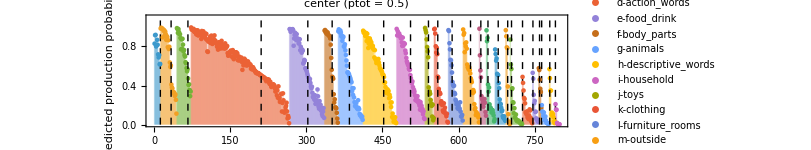

```mathematica
(*カテゴリー内でVoA順に並べた各語の推定表出確率．
Predicted production probabilities ordered by VoA within each category.*)
plotPtot=0.5;
orderedProbabilities=predict[zcenter3[plotPtot]][[orderbyvoa]];

orderedPoints=MapThread[Tooltip[{#1,#2},fitem4[#3]]&,{Range[Length[orderedProbabilities]],orderedProbabilities,orderbyvoa}];

centerWordProbabilityPlot=ListPlot[(orderedPoints[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word rank (VoA order within category)","Predicted production probability"},ImageSize->600,AspectRatio->1/4,PlotRange->{0,1.1},Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][plotPtot],0},{ptotToRank[nc][plotPtot],1.1}}]},{nc,Length[catn]}],PlotLegends->Placed[catname,Right],PlotLabel->Row[{"center"," (ptot = ",plotPtot,")"}]];

centerWordProbabilityPlot
```

#### 総語彙割合0.5における Left・Right・Out・In の語ごとの表出確率 Word-wise production probabilities at Left, Right, Out, and In for ptot = 0.5

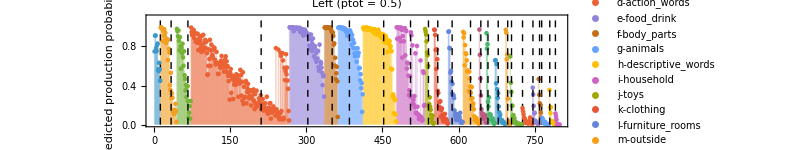
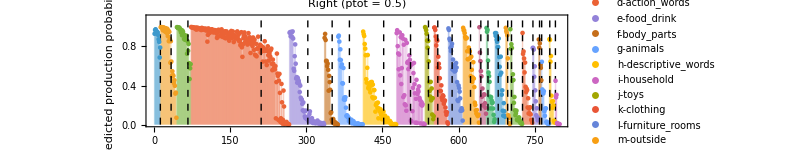
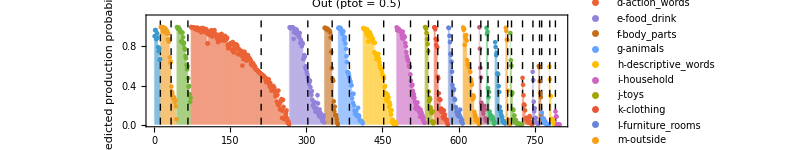
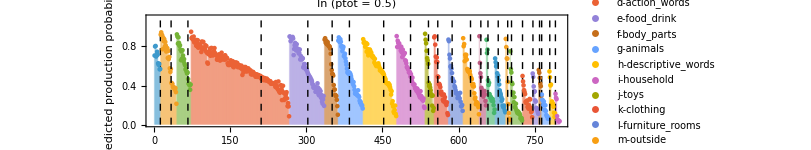

```mathematica
(*4本の軌道における語ごとの予測表出確率を描く．破線は中央軌道で求めた VoA が現在の ptot に対応する語順位置を示す．Plot word-wise predicted production probabilities for four trajectories.Dashed lines mark positions where center-trajectory VoA corresponds to the current ptot.*)wordProbabilityPlot[trajectory_,name_]:=Module[{probabilities,points},probabilities=predict[trajectory[plotPtot]][[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},fitem4[#3]]&,{Range[Length[probabilities]],probabilities,orderbyvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word rank (VoA order within category)","Predicted production probability"},PlotRange->{0,1.1},Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][plotPtot],0},{ptotToRank[nc][plotPtot],1.1}}]},{nc,Length[catn]}],AspectRatio->1/4,ImageSize->600,PlotLegends->Placed[catname,Right],PlotLabel->Row[{name," (ptot = ",plotPtot,")"}]]];

leftWordProbabilityPlot=wordProbabilityPlot[zleft3,"Left"];
rightWordProbabilityPlot=wordProbabilityPlot[zright3,"Right"];
outWordProbabilityPlot=wordProbabilityPlot[zout3,"Out"];
inWordProbabilityPlot=wordProbabilityPlot[zin3,"In"];

Column[{leftWordProbabilityPlot,rightWordProbabilityPlot,outWordProbabilityPlot,inWordProbabilityPlot},Spacings->2]
```

#### 異なる総語彙割合における Left–Right 軸（nominality）の語ごとの表出確率差 Word-wise production-probability differences along the Left–Right (nominality) axis at different total vocabulary proportions

各カテゴリーの破線は，VoA 順に並んだ語のうち，VoA が図の ptot と等しくなる語順位置を補間して示す．破線の左側には VoA が ptot より小さい語，右側には大きい語が並ぶ．

In each category, the dashed line marks the interpolated word position where VoA equals the plotted ptot . Words to its left have smaller VoA, and words to its right have larger VoA .

```mathematica
(*指定した総語彙割合で，Left−Right の語ごとの表出確率差を描く．Plot word-wise Left−Right production-probability differences at a specified total vocabulary proportion.*)Clear[leftRightDifferencePlotAt];

leftRightDifferencePlotAt[ptot_?NumericQ]:=Module[{values,points,yRange={-1.,1.}},values=(predict[zleft3[ptot]]-predict[zright3[ptot]])[[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},fitem4[#3]]&,{Range[Length[values]],values,orderbyvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Production probability (Left - Right)"},ImageSize->600,AspectRatio->1/2,PlotRange->yRange,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",ptot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][ptot],yRange[[1]]},{ptotToRank[nc][ptot],yRange[[2]]}}]},{nc,Length[catn]}]]];
```

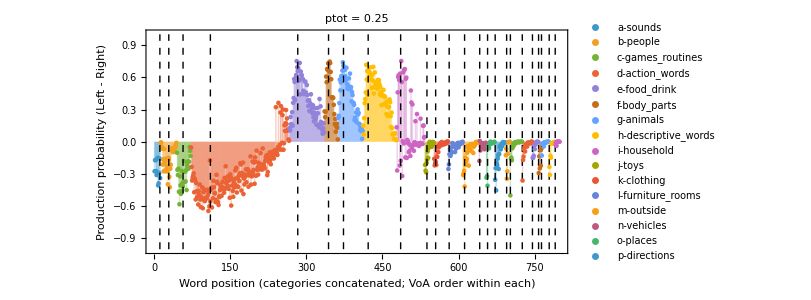

```mathematica
leftRightDifferencePlotAt[0.25]
```

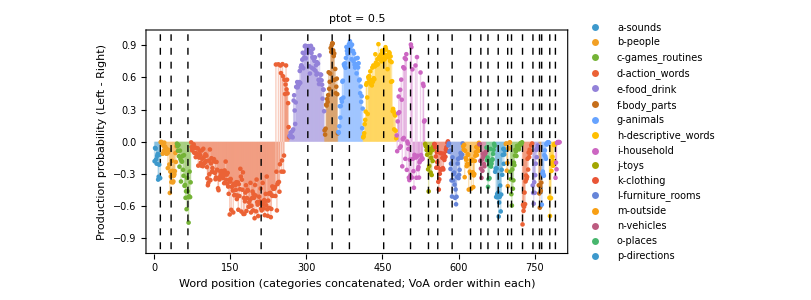

```mathematica
leftRightDifferencePlotAt[0.5]
```

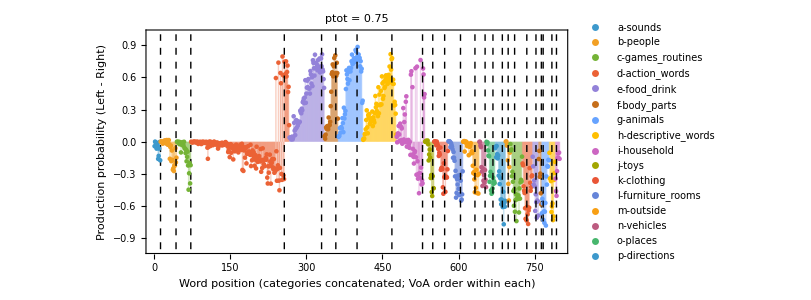

```mathematica
leftRightDifferencePlotAt[0.75]
```

```mathematica
listLR=Table[leftRightDifferencePlotAt[ptot],{ptot,0.1,0.9,0.1}];
```

```mathematica
ListAnimate[listLR]
```

```mathematica
(*videoPath=FileNameJoin[{NotebookDirectory[],"Mandarin_LeftRight_nominality_ptot_0p1_to_0p9.mp4"}];
Export[videoPath,listLR,"MP4",FrameRate->1]*)
```

#### 異なる総語彙割合における Out–In 軸（commonality）の語ごとの表出確率差 Word-wise production-probability differences along the Out–In (commonality) axis at different total vocabulary proportions

各カテゴリーの破線は，VoA 順に並んだ語のうち，VoA が図の ptot と等しくなる語順位置を補間して示す．破線の左側には VoA が ptot より小さい語，右側には大きい語が並ぶ．

In each category, the dashed line marks the interpolated word position where VoA equals the plotted ptot. Words to its left have smaller VoA, and words to its right have larger VoA.

```mathematica
(*指定した総語彙割合で，Out−In の語ごとの表出確率差を描く．Plot word-wise Out−In production-probability differences at a specified total vocabulary proportion.*)Clear[outInDifferencePlotAt];

outInDifferencePlotAt[ptot_?NumericQ]:=Module[{values,points,yRange={-1.,1.}},values=(predict[zout3[ptot]]-predict[zin3[ptot]])[[orderbyvoa]];
points=MapThread[Tooltip[{#1,#2},#3]&,{Range[Length[values]],values,itemsvoa}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Production probability (Out - In)"},ImageSize->600,AspectRatio->1/2,PlotRange->yRange,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",ptot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][ptot],yRange[[1]]},{ptotToRank[nc][ptot],yRange[[2]]}}]},{nc,Length[catn]}]]];
```

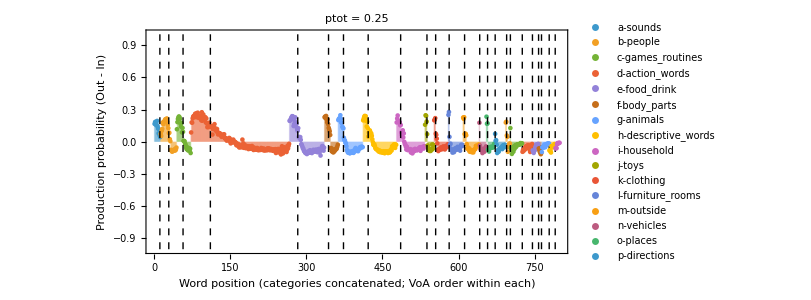

```mathematica
outInDifferencePlotAt[0.25]
```

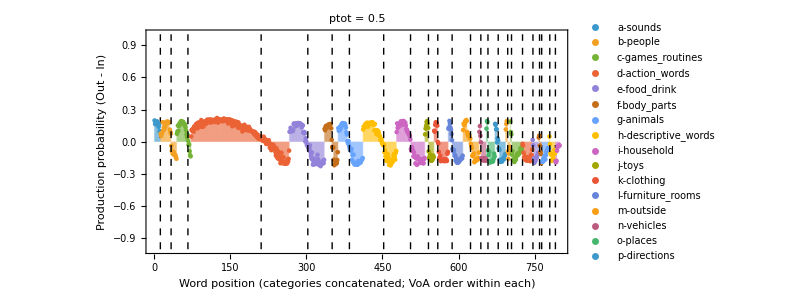

```mathematica
outInDifferencePlotAt[0.5]
```

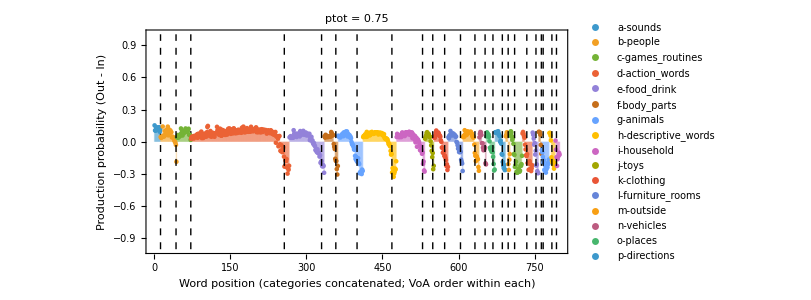

```mathematica
outInDifferencePlotAt[0.75]
```

```mathematica
listOI=Table[outInDifferencePlotAt[ptot],{ptot,0.1,0.9,0.1}];
```

```mathematica
ListAnimate[listOI]
```

```mathematica
(*
videoPath=FileNameJoin[{NotebookDirectory[],"Mandarin_OutIn_commonality_ptot_0p1_to_0p9.mp4"}];
Export[videoPath,listOI,"MP4",FrameRate->1]
*)
```

```mathematica
(*同じ総語彙割合における Out と In の表出確率の対数比を描く．Plot the log production-probability ratio of Out to In at the same total vocabulary proportion.*)(*logRatioPtot=0.5;
outProbabilities=predict[zout3[logRatioPtot]][[orderbyvoa]];
inProbabilities=predict[zin3[logRatioPtot]][[orderbyvoa]];
outInLogRatios=Log[outProbabilities/inProbabilities];
logRatioYRange=MinMax[outInLogRatios];
outInLogRatioPoints=MapThread[Tooltip[{#1,#2},#3]&,{Range[Length[outInLogRatios]],outInLogRatios,itemsvoa}];
outInLogRatioPlot=ListPlot[(outInLogRatioPoints[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Word position (categories concatenated; VoA order within each)","Log production-probability ratio (Out / In)"},ImageSize->600,AspectRatio->1/2,PlotRange->All,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",logRatioPtot}],Epilog->Table[{Dashed,Thin,Line[{{ptotToRank[nc][logRatioPtot],logRatioYRange[[1]]},{ptotToRank[nc][logRatioPtot],logRatioYRange[[2]]}}]},{nc,Length[catn]}]];
outInLogRatioPlot
*)
```

#### 元のCDI項目順における Left − Right の表出確率差（ptot = 0.5） Left-minus-Right production-probability difference in the original CDI item order (ptot = 0.5)

d-action_words と i-household のカテゴリー内で，差の符号が急に切り替わる箇所が見られる．この図はその現象を確認するために示す．原因は現時点で分かっていない．
The sign of the difference changes abruptly within the d-action_words and i-household categories. This plot documents that pattern; its cause is currently unknown.

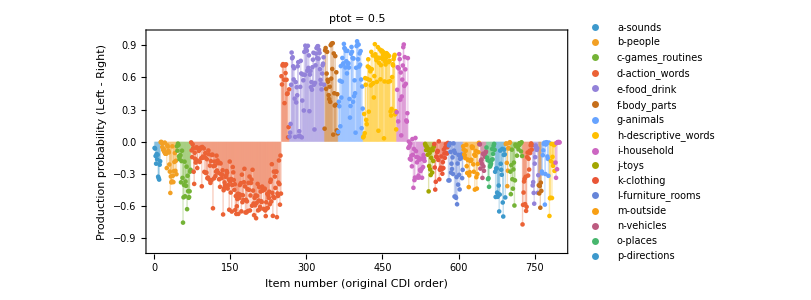

```mathematica
Module[{ptot=0.5,values,points,yRange={-1.,1.}},values=predict[zleft3[ptot]]-predict[zright3[ptot]];
points=MapThread[Tooltip[{#1,#2},fitem4[#1]]&,{Range[Length[values]],values}];
ListPlot[(points[[#[[1]];;#[[2]]]]&/@catn),Filling->Axis,Frame->True,FrameLabel->{"Item number (original CDI order)","Production probability (Left - Right)"},ImageSize->600,AspectRatio->1/2,PlotRange->yRange,PlotLegends->Placed[catname,Right],PlotLabel->Row[{"ptot = ",ptot}]]]
```

#### 元のCDI項目順における Left − Right 表出確率差の項目別一覧（ptot = 0.5） Item-wise Left-minus-Right production-probability differences in the original CDI order (ptot = 0.5)

```mathematica
voa=0.5;ztmp1=zleft3[voa];temp1=predict[ztmp1][[All]];ztmp2=zright3[voa];
temp2=predict[ztmp2][[All]];
diffLR={Range[799],temp1-temp2}ᵀ;
```

d-action_words では項目番号251，i-household では項目番号501の前後で，Left − Right の表出確率差 diffLR の符号が切り替わる．
以下の表で，その前後の値を元のCDI項目順に確認する．
The Left-minus-Right difference diffLR changes sign around item 251 in d-action_words and item 501 in i-household. The tables below show the surrounding values in the original CDI item order.

```mathematica
(*d-action_words の項目別一覧．
Item-wise differences in d-action_words.*)differenceTableHeaders=Style[#,Bold]&/@{"Item number","Category","Chinese word","CDI code","English translation","Left - Right"};

Grid[Prepend[(Append[fitem4[#],diffLR[[#,2]]]&/@Range[73,266]),differenceTableHeaders],Frame->All]
```

Item number | Category | Chinese word | CDI code | English translation | Left - Right
73 | d-action_words | 抱 | d1 | hug | -0.0060164
74 | d-action_words | 拿（过来） | d2 | bring | -0.0807969
75 | d-action_words | 来 | d3 | come | -0.143146
76 | d-action_words | 走 | d4 | walk | -0.0250378
77 | d-action_words | 坐 | d5 | sit | -0.0604244
78 | d-action_words | 站 | d6 | stand | -0.279211
79 | d-action_words | 蹲 | d7 | squat | -0.392334
80 | d-action_words | 尿 | d8 | pee | -0.102367
81 | d-action_words | 上 | d9 | up | -0.158882
82 | d-action_words | 下 | d10 | down | -0.193785
83 | d-action_words | 喝 | d11 | drink (action) | -0.055882
84 | d-action_words | 吃 | d12 | eat | -0.0518749
85 | d-action_words | 喂 | d13 | feed | -0.244681
86 | d-action_words | 爬 | d14 | climb | -0.176131
87 | d-action_words | 要 | d15 | need | -0.0654908
88 | d-action_words | 有 | d16 | have | -0.0847708
89 | d-action_words | 睡觉 | d17 | sleep | -0.0719067
90 | d-action_words | 盖上 | d18 | cover (action) | -0.18802
91 | d-action_words | 玩 | d19 | play | -0.0655457
92 | d-action_words | 开（门） | d20 | open (action) | -0.0542581
93 | d-action_words | 关 | d21 | close | -0.153153
94 | d-action_words | 画画 | d22 | draw | -0.41452
95 | d-action_words | 打 | d23 | hit | -0.0485657
96 | d-action_words | 背 | d24 | carry | -0.137801
97 | d-action_words | 戴 | d25 | wear | -0.147929
98 | d-action_words | 洗 | d26 | wash | -0.0619753
99 | d-action_words | 擦 | d27 | wipe | -0.280944
100 | d-action_words | 亲（一个） | d28 | kiss | -0.144026
101 | d-action_words | 飞 | d29 | fly (action) | -0.106199
102 | d-action_words | 亮了 | d30 | brighten | -0.290922
103 | d-action_words | 打开 | d31 | open (action) | -0.286961
104 | d-action_words | 起来 | d32 | get up | -0.161898
105 | d-action_words | 剥 | d33 | peel | -0.339634
106 | d-action_words | 叫 | d34 | cry | -0.33241
107 | d-action_words | 看 | d35 | look | -0.081311
108 | d-action_words | 跑 | d36 | run | -0.116704
109 | d-action_words | 跳 | d37 | jump | -0.353572
110 | d-action_words | 踢 | d38 | kick | -0.222251
111 | d-action_words | 倒（水） | d39 | pour | -0.382943
112 | d-action_words | 买 | d40 | buy | -0.180058
113 | d-action_words | 摸 | d41 | touch | -0.35798
114 | d-action_words | 穿 | d42 | wear | -0.123177
115 | d-action_words | 给 | d43 | give | -0.120063
116 | d-action_words | 送 | d44 | send | -0.619343
117 | d-action_words | 掉 | d45 | drop | -0.227715
118 | d-action_words | 笑 | d46 | smile | -0.340971
119 | d-action_words | 哭 | d47 | cry | -0.184696
120 | d-action_words | 拍 | d48 | clap | -0.222286
121 | d-action_words | 会 | d49 | can (auxiliary) | -0.31898
122 | d-action_words | 写 | d50 | write | -0.278502
123 | d-action_words | 躺 | d51 | lie down | -0.129305
124 | d-action_words | 趴 | d52 | lie down | -0.267216
125 | d-action_words | 骑 | d53 | ride | -0.174086
126 | d-action_words | 开（车） | d54 | drive | -0.199765
127 | d-action_words | 蹦 | d55 | hop | -0.290032
128 | d-action_words | 扫（地） | d56 | sweep | -0.349238
129 | d-action_words | 去 | d57 | go | -0.195508
130 | d-action_words | 放 | d58 | put | -0.419959
131 | d-action_words | 咬 | d59 | bite | -0.201982
132 | d-action_words | 扔 | d60 | throw | -0.302555
133 | d-action_words | 吐 | d61 | spit | -0.339642
134 | d-action_words | 说 | d62 | say | -0.306933
135 | d-action_words | 吹 | d63 | blow | -0.265371
136 | d-action_words | 追 | d64 | chase | -0.676886
137 | d-action_words | 摔 | d65 | fall | -0.451055
138 | d-action_words | 是（什么） | d66 | be | -0.432956
139 | d-action_words | 想 | d67 | think | -0.378596
140 | d-action_words | 知道 | d68 | know | -0.404987
141 | d-action_words | 梳 | d69 | comb (action) | -0.326904
142 | d-action_words | 刷 | d70 | brush (action) | -0.314185
143 | d-action_words | 唱 | d71 | sing | -0.27233
144 | d-action_words | 听 | d72 | hear | -0.28774
145 | d-action_words | 听见 | d73 | hear | -0.435497
146 | d-action_words | 扎 | d74 | prick | -0.404809
147 | d-action_words | 推 | d75 | push | -0.351481
148 | d-action_words | 捡 | d76 | pick up | -0.63267
149 | d-action_words | 找 | d77 | look for | -0.184421
150 | d-action_words | 倒了 | d78 | fall | -0.371403
151 | d-action_words | 进去 | d79 | enter | -0.472725
152 | d-action_words | 出去 | d80 | leave | -0.346441
153 | d-action_words | 过 | d81 | cross | -0.649609
154 | d-action_words | 回来 | d82 | return | -0.404094
155 | d-action_words | 踩 | d83 | step | -0.235575
156 | d-action_words | 藏 | d84 | hide | -0.284963
157 | d-action_words | 拉/拽 | d85 | pull | -0.356494
158 | d-action_words | 讲 | d86 | tell | -0.44777
159 | d-action_words | 握（手） | d87 | shake | -0.395387
160 | d-action_words | 敲 | d88 | knock | -0.633722
161 | d-action_words | 闭（眼、嘴） | d89 | close | -0.50527
162 | d-action_words | 丢 | d90 | lose | -0.672077
163 | d-action_words | 喜欢 | d91 | like | -0.600492
164 | d-action_words | 动 | d92 | move | -0.533312
165 | d-action_words | 等 | d93 | wait | -0.484683
166 | d-action_words | 醒 | d94 | wake | -0.671365
167 | d-action_words | 滑 | d95 | slide (action) | -0.48683
168 | d-action_words | 切（菜） | d96 | cut | -0.523718
169 | d-action_words | 剪 | d97 | cut | -0.40272
170 | d-action_words | 撕 | d98 | tear | -0.49385
171 | d-action_words | 洒 | d99 | splash | -0.385496
172 | d-action_words | 撒 | d100 | spill | -0.647921
173 | d-action_words | 响 | d101 | sound (action) | -0.306298
174 | d-action_words | 接 | d102 | receive | -0.562719
175 | d-action_words | 碰 | d103 | hit | -0.4983
176 | d-action_words | 蹬 | d104 | step | -0.542828
177 | d-action_words | 抓 | d105 | catch | -0.376707
178 | d-action_words | 搬 | d106 | move | -0.251907
179 | d-action_words | 端 | d107 | carry | -0.415874
180 | d-action_words | 揉 | d108 | rub | -0.657883
181 | d-action_words | 转 | d109 | spin | -0.540624
182 | d-action_words | 爱 | d110 | love | -0.657785
183 | d-action_words | 乐（一个） | d111 | smile | -0.554517
184 | d-action_words | 数数 | d112 | count | -0.441181
185 | d-action_words | 磕 | d113 | knock | -0.643969
186 | d-action_words | 翻 | d114 | flip | -0.382827
187 | d-action_words | 夹 | d115 | pick | -0.447623
188 | d-action_words | 闻 | d116 | smell | -0.324149
189 | d-action_words | 尝 | d117 | taste | -0.639538
190 | d-action_words | 咽 | d118 | swallow | -0.499999
191 | d-action_words | 做饭 | d119 | cook | -0.383472
192 | d-action_words | 跳舞 | d120 | dance | -0.351835
193 | d-action_words | 换 | d121 | exchange | -0.595456
194 | d-action_words | 抹（油等） | d122 | wipe | -0.260885
195 | d-action_words | 装 | d123 | fill | -0.45449
196 | d-action_words | 摘（揪） | d124 | pick | -0.574472
197 | d-action_words | 让 | d125 | let | -0.683433
198 | d-action_words | 修 | d126 | fix | -0.522557
199 | d-action_words | 使劲 | d127 | Missing[NotAvailable] | -0.591428
200 | d-action_words | 举 | d128 | lift (action) | -0.500006
201 | d-action_words | 挂 | d129 | hang | -0.711717
202 | d-action_words | 滚 | d130 | roll (action) | -0.570519
203 | d-action_words | 挖 | d131 | dig | -0.503601
204 | d-action_words | 扶 | d132 | support | -0.392143
205 | d-action_words | 学 | d133 | learn | -0.638946
206 | d-action_words | 记（得） | d134 | remember | -0.547442
207 | d-action_words | 打破/打碎 | d135 | break | -0.422322
208 | d-action_words | 扭 | d136 | twist | -0.62857
209 | d-action_words | 停 | d137 | stop | -0.605768
210 | d-action_words | 压 | d138 | squeeze | -0.463127
211 | d-action_words | 撞 | d139 | bump | -0.552723
212 | d-action_words | 插 | d140 | insert | -0.562255
213 | d-action_words | 搂 | d141 | hug | -0.417018
214 | d-action_words | 带 | d142 | bring | -0.4549
215 | d-action_words | 搭 | d143 | ride | -0.437286
216 | d-action_words | 跟着 | d144 | follow | -0.625036
217 | d-action_words | 拨（电话） | d145 | call | -0.446575
218 | d-action_words | 逗 | d146 | amuse | -0.436364
219 | d-action_words | 排（队） | d147 | queue | -0.639148
220 | d-action_words | 干（什么） | d148 | do | -0.691909
221 | d-action_words | 用 | d149 | use | -0.562797
222 | d-action_words | 舔 | d150 | lick | -0.621216
223 | d-action_words | 嚼 | d151 | chew | -0.48545
224 | d-action_words | 拐（弯） | d152 | turn | -0.616108
225 | d-action_words | 弯 | d153 | bend | -0.498902
226 | d-action_words | 抢 | d154 | grab | -0.523172
227 | d-action_words | 眨（眼） | d155 | blink | -0.464866
228 | d-action_words | 拧 | d156 | wind | -0.581603
229 | d-action_words | 叫唤 | d157 | shout | -0.374016
230 | d-action_words | 瞧 | d158 | look | -0.353219
231 | d-action_words | 弄 | d159 | make | -0.555606
232 | d-action_words | 游泳 | d160 | swim | -0.209197
233 | d-action_words | 贴 | d161 | stick | -0.475893
234 | d-action_words | 拔（草） | d162 | pick | -0.68981
235 | d-action_words | 长（大） | d163 | grow | -0.511879
236 | d-action_words | 套 | d164 | cover (action) | -0.278056
237 | d-action_words | 拆 | d165 | break | -0.523215
238 | d-action_words | 读 | d166 | read | -0.323715
239 | d-action_words | 搁 | d167 | put | -0.429755
240 | d-action_words | 瞅 | d168 | look | -0.278456
241 | d-action_words | 逮（坏蛋） | d169 | catch | -0.278349
242 | d-action_words | 躲 | d170 | hide | -0.701973
243 | d-action_words | 待（一会儿） | d171 | wait | -0.481216
244 | d-action_words | 嚷 | d172 | shout | -0.504756
245 | d-action_words | 问 | d173 | ask | -0.380342
246 | d-action_words | 告诉 | d174 | tell | -0.174181
247 | d-action_words | 捋/挽（袖子） | d175 | tug | -0.394798
248 | d-action_words | 冲 | d176 | rinse | -0.585401
249 | d-action_words | 帮助/帮忙 | d177 | help | -0.128642
250 | d-action_words | 拖 | d178 | pull | -0.482575
251 | d-action_words | 悠 | d179 | swing (action) | 0.609868
252 | d-action_words | 绑 | d180 | tie (action) | 0.533034
253 | d-action_words | 搅 | d181 | stir | 0.709998
254 | d-action_words | 绕 | d182 | go around | 0.722272
255 | d-action_words | 摁（按） | d183 | press | 0.7188
256 | d-action_words | 做梦 | d184 | dream | 0.577384
257 | d-action_words | 工作 | d185 | work (action) | 0.359491
258 | d-action_words | 试 | d186 | try | 0.709551
259 | d-action_words | 卖 | d187 | sell | 0.638996
260 | d-action_words | 掸掸 | d188 | wipe | 0.72065
261 | d-action_words | 收拾 | d189 | clean (action) | 0.576836
262 | d-action_words | 忘记 | d190 | forget | 0.444347
263 | d-action_words | 假装 | d191 | pretend | 0.450223
264 | d-action_words | 希望 | d192 | hope | 0.0418078
265 | d-action_words | 抖搂 | d193 | shake | 0.136179
266 | d-action_words | 蹭 | d194 | rub | 0.487475

```mathematica
(*i-household の項目別一覧．Item-wise differences in i-household.*)householdlist=Grid[Prepend[(Append[fitem4[#],diffLR[[#,2]]]&/@Range[478,533]),differenceTableHeaders],Frame->All]
```

Item number | Category | Chinese word | CDI code | English translation | Left - Right
478 | i-household | 碗 | i1 | bowl | 0.274952
479 | i-household | 杯子 | i2 | cup | 0.48366
480 | i-household | 瓶子 | i3 | bottle | 0.69378
481 | i-household | 勺 | i4 | spoon | 0.189507
482 | i-household | 筷子 | i5 | chopstick | 0.682032
483 | i-household | 盘 | i6 | plate | 0.815062
484 | i-household | 锅 | i7 | pot | 0.768847
485 | i-household | 刀 | i8 | knife | 0.39132
486 | i-household | 茶杯 | i9 | cup | 0.644606
487 | i-household | 灯 | i10 | lamp | 0.0591452
488 | i-household | 钟/表 | i11 | clock | 0.421096
489 | i-household | 电话 | i12 | telephone | 0.57822
490 | i-household | 电扇 | i13 | fan | 0.709615
491 | i-household | 电池 | i14 | battery | 0.880292
492 | i-household | 手表 | i15 | watch (object) | 0.905239
493 | i-household | 收音机 | i16 | radio | 0.519522
494 | i-household | 照相机 | i17 | camera | 0.787773
495 | i-household | （钢）琴 | i18 | piano | 0.673884
496 | i-household | 录音机 | i19 | voice recorder | 0.539271
497 | i-household | 音响 | i20 | stereo | 0.198362
498 | i-household | VCD机 | i21 | Missing[NotAvailable] | 0.187639
499 | i-household | 被子 | i22 | blanket | 0.265784
500 | i-household | 枕头 | i23 | pillow | 0.778362
501 | i-household | 药 | i24 | medicine | -0.0568285
502 | i-household | 梳子/栊子 | i25 | comb (object) | 0.00224123
503 | i-household | 盆 | i26 | basin | -0.0429023
504 | i-household | 肥皂/香皂 | i27 | soap | -0.158943
505 | i-household | 牙刷 | i28 | toothbrush | -0.0168112
506 | i-household | 毛巾 | i29 | towel | -0.166806
507 | i-household | 手纸 | i30 | tissue | -0.130394
508 | i-household | 画 | i31 | picture | -0.228829
509 | i-household | 纸 | i32 | paper | 0.025026
510 | i-household | 剪刀 | i33 | scissors | -0.121819
511 | i-household | 绳 | i34 | rope | -0.428436
512 | i-household | 眼镜 | i35 | glasses | -0.0668797
513 | i-household | 报纸 | i36 | newspaper | -0.357167
514 | i-household | 钥匙 | i37 | key | -0.333233
515 | i-household | 钱 | i38 | money | 0.0353507
516 | i-household | 包 | i39 | bag | -0.0879595
517 | i-household | 书包 | i40 | bag | -0.142371
518 | i-household | 钱包 | i41 | purse | -0.191447
519 | i-household | 口袋 | i42 | pocket | -0.333341
520 | i-household | 扇子 | i43 | fan | -0.146657
521 | i-household | （抹）布 | i44 | cloth | -0.31501
522 | i-household | 盒子 | i45 | box | -0.333237
523 | i-household | 篮子 | i46 | basket | -0.16638
524 | i-household | 桶 | i47 | bucket | -0.261729
525 | i-household | 刷子 | i48 | brush (object) | -0.273674
526 | i-household | 笤帚 | i49 | broom | -0.158187
527 | i-household | 托把/墩布 | i50 | rag | -0.255454
528 | i-household | 垃圾 | i51 | trash | -0.335206
529 | i-household | 簸箕 | i52 | dustpan | -0.159269
530 | i-household | 锤子 | i53 | hammer | -0.235926
531 | i-household | 钉子 | i54 | nail (object) | -0.124111
532 | i-household | 木头 | i55 | wood | -0.151987
533 | i-household | 东西 | i56 | thing | -0.178589

#### 等総語彙割合面上の5つの発達軌道位置 Five developmental-trajectory positions on an equal-vocabulary-proportion surface

```mathematica
(*後続のサンプル生成で用いる5つの軌道位置を再表示する．
Redisplay the five trajectory positions used for subsequent sampling.*)trajectoryOverviewPlot
```

-Graphics3D-

#### 軌道周辺の局所事後標準偏差と潜在点生成 Local posterior standard deviations and latent-point generation around trajectories

```mathematica
(*潜在点 z に最も近い3名のCDIプロフィールを選び，Encoderの事後標準偏差を潜在次元ごとに平均する．Select the three CDI profiles nearest to latent point z and average their encoder posterior standard deviations separately for each latent dimension.*)
Clear[nearestProfileIndices,z2σ];

nNearestProfiles=3;
nearestProfileIndices[z_]:=TakeSmallestBy[Range[Length[zdatasort]],Norm[z-zdatasort[[#]]]&,nNearestProfiles];

z2σ[z_]:=Module[{nearestIndices,nearestProfiles},nearestIndices=nearestProfileIndices[z];
nearestProfiles=alldatasort[[nearestIndices+1,5;;]];
Mean[Exp[0.5 tologsigma[#]]&/@nearestProfiles]];
```

```mathematica
(*軌道上の点 zc を中心とし，近傍3名から推定した 事後標準偏差を用いて潜在点を生成する．seed を固定する．Generate latent points around trajectory point zc using posterior standard deviations estimated from the three nearest CDI profiles,with a fixed seed.*)
Clear[generate];

generate[zc_,num_,seed_]:=BlockRandom[SeedRandom[seed,Method->"MersenneTwister"];
RandomVariate[MultinormalDistribution[zc,DiagonalMatrix[z2σ[zc]^2]],num]];
```

#### 引き戻し前の生成サンプルと等総語彙割合面 Generated samples before projection and the equal-total-vocabulary-proportion surface

```mathematica
(*Out 軌道上の点を中心にサンプルを生成し，引き戻し前の位置を確認する．Generate samples around a point on the Out trajectory and inspect their positions before projection.*)ptot=0.5;
zwork=zout3[ptot];
rawSamples=generate[zwork,100,9999];

localUncertaintyPlot=ListPointPlot3D[{MapThread[Around,{zwork,z2σ[zwork]}]},PlotStyle->Directive[Blue,PointSize[0.01],Thickness[0.003]]];

rawSamplePlot=ListPointPlot3D[rawSamples,PlotStyle->Directive[Blue,PointSize[0.008]]];

targetPtotSurface=ListContourPlot3D[gridall,Contours->{ptot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

trajectoryPointsAtPtot=<|"Center"->zcenter3[ptot],"Left"->zleft3[ptot],"Right"->zright3[ptot],"In"->zin3[ptot],"Out"->zout3[ptot]|>;

trajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

trajectoryPointGraphic=Graphics3D[KeyValueMap[{trajectoryColors[#1],PointSize[0.02],Point[#2]}&,trajectoryPointsAtPtot]];

rawSampleDeviationPlot=Show[localUncertaintyPlot,rawSamplePlot,targetPtotSurface,Graphics3D[{{Black,PointSize[0.03],Point[zAllZero]},{Red,PointSize[0.03],Point[zAllOne]}}],trajectoryPointGraphic,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{0.0,-3,3},ImageSize->400]
```

-Graphics3D-

```mathematica
(*引き戻し前の生成サンプルについて，総語彙数の統計量を計算する．Calculate total vocabulary statistics for generated samples before projection.*)
ClearAll[rawSampleVocabularyStats];

Options[rawSampleVocabularyStats]={"Ptot"->0.5,"NSamples"->100,"Seed"->9999};

rawSampleVocabularyStats[trajectoryFunction_,OptionsPattern[]]:=Module[{ptot,nSamples,seed,latentCenter,generatedSamples,vocabularyTotals,targetVocabulary,meanVocabulary,absoluteDeviations},ptot=OptionValue["Ptot"];
nSamples=OptionValue["NSamples"];
seed=OptionValue["Seed"];
latentCenter=trajectoryFunction[ptot];
generatedSamples=generate[latentCenter,nSamples,seed];
vocabularyTotals=Total/@(predict/@generatedSamples);
targetVocabulary=Total[predict[latentCenter]];
meanVocabulary=Mean[vocabularyTotals];
absoluteDeviations=Abs[vocabularyTotals-targetVocabulary];
<|"CenterVocabulary"->targetVocabulary,"Mean"->meanVocabulary,"SD"->StandardDeviation[vocabularyTotals],"Max"->Max[vocabularyTotals],"Min"->Min[vocabularyTotals],"MaxMinusMean"->Max[vocabularyTotals]-meanVocabulary,"MinMinusMean"->Min[vocabularyTotals]-meanVocabulary,"MaxRelativeDeviation"->(Max[vocabularyTotals]-meanVocabulary)/meanVocabulary,"MinRelativeDeviation"->(Min[vocabularyTotals]-meanVocabulary)/meanVocabulary,"MeanAbsoluteDeviationFromTarget"->Mean[absoluteDeviations],"SDAbsoluteDeviationFromTarget"->StandardDeviation[absoluteDeviations]|>];
```

```mathematica
(*５本の軌道について，引き戻し前の生成サンプルを集計する．Calculate statistics for samples generated before projection around each of the five trajectories.*)trajectoryFunctionsForDeviation=<|"Center"->zcenter3,"Left"->zleft3,"Right"->zright3,"In"->zin3,"Out"->zout3|>;
rawSampleStatsByTrajectory=Map[rawSampleVocabularyStats[#,"Ptot"->0.5,"NSamples"->100,"Seed"->9999]&,trajectoryFunctionsForDeviation];

Keys[rawSampleStatsByTrajectory]
```

{Center,Left,Right,In,Out}

```mathematica
(*５本の軌道で，引き戻し前のサンプルの総語彙数を比較する．Compare total vocabulary sizes of samples before projection across the five trajectories.*)rawSampleDeviationRows=KeyValueMap[Function[{position,statistics},{position,statistics["CenterVocabulary"],statistics["Mean"],statistics["SD"],statistics["Max"],statistics["Min"],statistics["MaxMinusMean"],statistics["MinMinusMean"],100 statistics["MaxRelativeDeviation"],100 statistics["MinRelativeDeviation"],statistics["MeanAbsoluteDeviationFromTarget"],statistics["SDAbsoluteDeviationFromTarget"]}],rawSampleStatsByTrajectory];

rawSampleDeviationTable=Grid[Prepend[rawSampleDeviationRows,{"Position","Target","Mean","SD","Max","Min","Max - Mean","Min - Mean","Max - Mean (%)","Min - Mean (%)","Mean |Sample - Target|","SD |Sample - Target|"}],Frame->All]
```

Position | Target | Mean | SD | Max | Min | Max - Mean | Min - Mean | Max - Mean (%) | Min - Mean (%) | Mean |Sample - Target| | SD |Sample - Target|
Center | 399.47 | 401.157 | 16.8697 | 436.758 | 364.893 | 35.6008 | -36.2643 | 8.87453 | -9.03992 | 14.0123 | 9.44117
Left | 399.624 | 400.523 | 10.6978 | 425.807 | 375.091 | 25.2843 | -25.4319 | 6.31284 | -6.34968 | 8.67579 | 6.26329
Right | 399.499 | 400.197 | 16.2777 | 434.023 | 366.126 | 33.8257 | -34.071 | 8.45225 | -8.51354 | 13.6332 | 8.81553
In | 399.372 | 402.593 | 31.324 | 468.042 | 326.289 | 65.4492 | -76.3035 | 16.2569 | -18.953 | 25.9533 | 17.6436
Out | 399.487 | 400.358 | 8.98678 | 419.388 | 382.696 | 19.03 | -17.6623 | 4.75325 | -4.41163 | 7.49374 | 4.98044

#### 生成点を指定した等総語彙割合面へ移動する Moving generated points onto a specified equal-total-vocabulary-proportion surface

```mathematica
(*出発点における総語彙割合の勾配方向に沿う直線上を移動し，指定した等総語彙割合面との交点を求める．Move along the line defined by the gradient of total vocabulary proportion at the starting point and find its intersection with the specified equal-total-vocabulary-proportion surface.*)
```

```mathematica
movedPt[startpt_,ptot_]:= Module[{vec,x,y,z,init,normalv,vec1,ptot1,ans,ansvec},
vec={x,y,z};
init=Rule@@@Transpose[{vec,startpt}];
normalv=Normalize[Grad[fall[x,y,z],{x,y,z}]/.init];
vec1[t_]:= startpt + normalv t;
ptot1[t_] := Flatten[fall[#[[1]],#[[2]],#[[3]]]&/@{vec1[t]}][[1]];
    ans=FindRoot[ptot1[t]==ptot,{t,0.}];
ansvec = vec1[t]/.ans
]
```

#### 指定した等総語彙割合面上での潜在サンプル生成 Generating latent samples on a specified equal-total-vocabulary-proportion surface

```mathematica
(*目標割合 ptot に対応する軌道上の点 zc の周囲に num 個の潜在点を生成し，同じ ptot の等総語彙割合面へ引き戻す．Generate num latent points around trajectory point zc at the target proportion ptot,then project them onto the same ptot isosurface.*)
```

```mathematica
createZdata[zc_,ptot_,num_,seed_]:=
Module[{sample},sample=generate[zc,num,seed];
movedPt[#,ptot]&/@sample]
```

#### 引き戻し後の潜在サンプルと等総語彙割合面 Projected latent samples on the equal-total-vocabulary-proportion surface

```mathematica
(*Left 軌道上で生成し，ptot=0.9 の面へ引き戻した潜在点を表示する．Show latent samples generated around the Left trajectory and projected onto the ptot=0.9 isosurface.*)projectedExamplePtot=0.9;
projectedExampleCenter=zleft3[projectedExamplePtot];

projectedExampleSamples=createZdata[projectedExampleCenter,projectedExamplePtot,100,999];

projectedUncertaintyPlot=ListPointPlot3D[{MapThread[Around,{projectedExampleCenter,z2σ[projectedExampleCenter]}]},PlotStyle->Directive[Blue,PointSize[0.01],Thickness[0.003]]];

projectedSamplePlot=ListPointPlot3D[projectedExampleSamples,PlotStyle->Directive[Blue,PointSize[0.008]]];

projectedTargetSurface=ListContourPlot3D[gridall,Contours->{projectedExamplePtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

projectedTrajectoryPoints=<|"Center"->zcenter3[projectedExamplePtot],"Left"->zleft3[projectedExamplePtot],"Right"->zright3[projectedExamplePtot],"In"->zin3[projectedExamplePtot],"Out"->zout3[projectedExamplePtot]|>;

projectedTrajectoryColors=<|"Center"->Green,"Left"->Magenta,"Right"->Cyan,"In"->Cyan,"Out"->Magenta|>;

projectedTrajectoryGraphic=Graphics3D[KeyValueMap[{projectedTrajectoryColors[#1],PointSize[0.02],Point[#2]}&,projectedTrajectoryPoints]];

projectedSampleSurfacePlot=Show[projectedUncertaintyPlot,projectedSamplePlot,projectedTargetSurface,Graphics3D[{{Black,PointSize[0.03],Point[zAllZero]},{Red,PointSize[0.03],Point[zAllOne]}}],projectedTrajectoryGraphic,BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{1.0,-3,1},ImageSize->400]
```

-Graphics3D-

#### 5本の発達軌道に沿った合成CDIプロファイルの生成 Generation of synthetic CDI profiles along the five developmental trajectories

```mathematica
(*軌道とptot水準ごとに再現可能な乱数seedを定める．
Define reproducible random seeds for each trajectory and ptot level.*)
seedIn[k_]:=Hash[{"in",k},"SHA256"]
seedOut[k_]:=Hash[{"out",k},"SHA256"]
seedLeft[k_]:=Hash[{"Left",k},"SHA256"]
seedRight[k_]:=Hash[{"right",k},"SHA256"]
seedCenter[k_]:=Hash[{"center",k},"SHA256"]
```

```mathematica
(*１本の軌道について，ptot=0.1～0.9 の各水準で潜在点を生成し，Decoder の出力を付けた合成 CDI データ行を作る．For one trajectory,generate latent points at each ptot level from 0.1 to 0.9 and append the decoder outputs to form synthetic CDI data rows.*)ClearAll[generateTrajectoryCDIRows];

generateTrajectoryCDIRows[trajectoryFunction_,seedFunction_,numSamples_Integer:100]:=Flatten[Table[Module[{ptot=k/10.,latentSamples,cdiSamples},latentSamples=createZdata[trajectoryFunction[ptot],ptot,numSamples,seedFunction[k]];
cdiSamples=predict/@latentSamples;
Transpose[Join[{ConstantArray[ptot,numSamples]},Transpose[latentSamples],Transpose[cdiSamples]]]],{k,1,9}],1];
```

```mathematica
(*５本の軌道を，対応する seed 関数と組にする．Associate each trajectory with its seed function.*)trajectoryGenerationSpecifications=<|"Center"->{zcenter3,seedCenter},"Left"->{zleft3,seedLeft},"Right"->{zright3,seedRight},"In"->{zin3,seedIn},"Out"->{zout3,seedOut}|>;
```

```mathematica
(*５本の軌道について合成 CDI データを作り，列名を付ける．Generate synthetic CDI data for the five trajectories and attach the column names.*)syntheticCDIRowsByTrajectory=Map[generateTrajectoryCDIRows[#[[1]],#[[2]],100]&,trajectoryGenerationSpecifications];

syntheticCDIColumns=Join[{"pTot","Zx","Zy","Zz"},alldata[[1,5;;]]];

syntheticCDIDataByTrajectory=Map[Prepend[#,syntheticCDIColumns]&,syntheticCDIRowsByTrajectory];
```

```mathematica
(*後続の解析で使う従来の変数名に，各軌道のデータを代入する．Assign each trajectory dataset to the names used later in the notebook.*)ZCDIcenter=syntheticCDIDataByTrajectory["Center"];
ZCDIleft=syntheticCDIDataByTrajectory["Left"];
ZCDIright=syntheticCDIDataByTrajectory["Right"];
ZCDIin=syntheticCDIDataByTrajectory["In"];
ZCDIout=syntheticCDIDataByTrajectory["Out"];
```

```mathematica
(* 
Export["ZCDIoutMandarin.csv",ZCDIout];
 Export["ZCDIinMandarin.csv",ZCDIin];
Export["ZCDIleftMandarin.csv",ZCDIleft];
Export["ZCDIrightMandarin.csv",ZCDIright];
Export["ZCDIcenterMandarin.csv",ZCDIcenter];
*)
```

#### システマティックに生成した潜在サンプルの確認 Verification of systematically generated latent samples

```mathematica
(*系統的に生成した In 軌道の潜在点が，対応する等総語彙割合面上にあることを代表例で確認する．Verify with a representative example that systematically generated latent samples on the In trajectory lie on the corresponding equal-total-vocabulary-proportion surface.*)
representativeSyntheticTrajectory="In";
representativeSyntheticPtot=0.4;

representativeSyntheticRows=Select[Rest[syntheticCDIDataByTrajectory[representativeSyntheticTrajectory]],Abs[#[[1]]-representativeSyntheticPtot]<10^-12&];

representativeSyntheticCoordinates=representativeSyntheticRows[[All,2;;4]];

representativeSyntheticCenter=trajectoryGenerationSpecifications[representativeSyntheticTrajectory][[1]][representativeSyntheticPtot];

representativeSyntheticSamplePlot=ListPointPlot3D[representativeSyntheticCoordinates,PlotStyle->Directive[Blue,PointSize[0.008]]];

representativeSyntheticSurface=ListContourPlot3D[gridall,Contours->{representativeSyntheticPtot},ContourStyle->Directive[cl[[2]],Opacity[0.2]]];

systematicGenerationCheckPlot=Show[representativeSyntheticSamplePlot,representativeSyntheticSurface,Graphics3D[{Darker[Green],PointSize[0.03],Point[representativeSyntheticCenter]}],BoxRatios->1,PlotRange->{{-6,6},{-6,6},{-6,6}},AxesLabel->{Style["z1",16],Style["z2",16],Style["z3",16]},ViewPoint->{0,-2,3}]
```

-Graphics3D-